# Method Of Estimating Beam Size From VELA Screen Images

This notebook is an accompaniment to the ‘Method Of Estimating Beam Size From VELA Screen Images’ report. It has been annotated to explain how all of the functions in the prgram work.
Duncan Scott & Tim Price & Matt Toplis

## Function Declarations

All functions and options needed for the analyisis are defined in this section.

## Options

### Plot Options

Set all of the options for the different types of plots used throughout the program here. I have tried to keep a consistent style for all plots.

```mathematica
(* Include the Needs["ErrorBarPlots"] command to include the ErrorListPlot function*)
Needs["ErrorBarPlots`"]
```

```mathematica
SetOptions[ListPlot,{AspectRatio->0.4,PlotStyle->{Red,Green,Blue,Black},Frame->True,FrameStyle->Thick,Axes->False,BaseStyle->{FontFamily->"Helvetica",FontSize->18},ImageSize->500,GridLines->None,Joined->True,PlotRange->All,FrameLabel->{"x","y"}}];
```

```mathematica
SetOptions[ErrorListPlot,{AspectRatio->0.4,PlotStyle->{Red,Green,Blue,Black},Frame->True,FrameStyle->Thick,Axes->False,BaseStyle->{FontFamily->"Helvetica",FontSize->18},ImageSize->500,GridLines->None,Joined->True,PlotRange->All,FrameLabel->{"x","y"}}];
```

```mathematica
SetOptions[ListLogPlot,{AspectRatio->0.4,PlotStyle->{Red,Green,Blue,Black},Frame->True,FrameStyle->Thick,Axes->False,BaseStyle->{FontFamily->"Helvetica",FontSize->18},ImageSize->500,GridLines->None,Joined->True,PlotRange->All,FrameLabel->{"x","y"}}];
```

```mathematica
SetOptions[Plot,{AspectRatio->0.4,PlotStyle->{Red,Green,Blue,Black},Frame->True,FrameStyle->Thick,Axes->False,BaseStyle->{FontFamily->"Helvetica",FontSize->18},ImageSize->500,GridLines->None,PlotRange->All,FrameLabel->{"x","y"}}];
```

```mathematica
SetOptions[LogLogPlot,{AspectRatio->0.4,PlotStyle->{Red,Green,Blue,Black},Frame->True,FrameStyle->Thick,Axes->False,BaseStyle->{FontFamily->"Helvetica",FontSize->18},ImageSize->500,GridLines->None,PlotRange->All,FrameLabel->{"x","y"}}];
```

```mathematica
SetOptions[ArrayPlot,{BaseStyle->{FontFamily->"Helvetica",FontSize->18},ImageSize->500,DataReversed->True,FrameTicks->Automatic,ColorFunction->"SunsetColors"}];
```

```mathematica
SetOptions[ListPlot3D,{BaseStyle->{FontFamily->"Helvetica",FontSize->18},ImageSize->500,PlotRange->All}];
```

## Compiler

Set the options for the compiler in this section, such as how many iterations before compiling basic functions.

```mathematica
Cases["CompileOptions"/.SystemOptions["CompileOptions"],opt:(s_String->_)/;StringMatchQ[s,__~~"Length"]]
SetSystemOptions["CompileOptions"->{"FoldCompileLength"->2,"TableCompileLength"->2,"NestCompileLength"->100,"MapCompileLength"->2,"ListableFunctionCompileLength"->2}]
```

{ApplyCompileLength→∞,ArrayCompileLength→250,FoldCompileLength→2,ListableFunctionCompileLength→2,MapCompileLength→2,NestCompileLength→100,ProductCompileLength→250,SumCompileLength→250,TableCompileLength→2}

CompileOptions→{ApplyCompileLength→∞,ArrayCompileLength→250,AutoCompileAllowCoercion→False,AutoCompileProtectValues→False,AutomaticCompile→False,BinaryTensorArithmetic→False,CompileAllowCoercion→True,CompileConfirmInitializedVariables→True,CompiledFunctionArgumentCoercionTolerance→2.10721,CompiledFunctionMaxFailures→3,CompileDynamicScoping→False,CompileEvaluateConstants→True,CompileOptimizeRegisters→False,CompileParallelizationThreshold→10,CompileReportCoercion→False,CompileReportExternal→False,CompileReportFailure→False,CompileValuesLast→True,FoldCompileLength→2,InternalCompileMessages→False,ListableFunctionCompileLength→2,MapCompileLength→2,NestCompileLength→100,NumericalAllowExternal→False,ProductCompileLength→250,ReuseTensorRegisters→True,SumCompileLength→250,SystemCompileOptimizations→All,TableCompileLength→2}

```mathematica
Compile`CompilerFunctions[]//Sort
```

{Abs,AddTo,And,Append,AppendTo,Apply,ArcCos,ArcCosh,ArcCot,ArcCoth,ArcCsc,ArcCsch,ArcSec,ArcSech,ArcSin,ArcSinh,ArcTan,ArcTanh,Arg,Array,ArrayDepth,Internal`Bag,Internal`BagPart,BitAnd,BitNot,BitOr,BitXor,Block,BlockRandom,Boole,Break,Cases,Catch,Ceiling,Chop,Internal`CompileError,System`Private`CompileSymbol,Complement,ComposeList,CompoundExpression,Conjugate,ConjugateTranspose,Continue,Cos,Cosh,Cot,Coth,Count,Csc,Csch,Decrement,Delete,DeleteCases,Dimensions,Divide,DivideBy,Do,Dot,Drop,Equal,Erf,Erfc,EvenQ,Exp,Internal`Expm1,Fibonacci,First,FixedPoint,FixedPointList,Flatten,NDSolve`FEM`FlattenAll,Floor,Fold,FoldList,For,FractionalPart,FreeQ,Gamma,Compile`GetElement,Goto,Greater,GreaterEqual,Gudermannian,Haversine,If,Im,Implies,Increment,Indexed,Inequality,Compile`InnerDo,Insert,IntegerDigits,IntegerPart,Intersection,InverseGudermannian,InverseHaversine,Compile`IteratorCount,Join,Label,Last,Length,Less,LessEqual,List,Log,Log10,Internal`Log1p,Log2,LogGamma,LogisticSigmoid,LucasL,Map,MapAll,MapAt,MapIndexed,MapThread,NDSolve`FEM`MapThreadDot,MatrixQ,Max,MemberQ,Min,Minus,Mod,Compile`Mod1,Module,Most,N,Negative,Nest,NestList,NonNegative,Not,OddQ,Or,OrderedQ,Out,Outer,Part,Partition,Piecewise,Plus,Position,Positive,Power,PreDecrement,PreIncrement,Prepend,PrependTo,Product,Quotient,Ramp,Random,RandomChoice,RandomComplex,RandomInteger,RandomReal,RandomSample,RandomVariate,Range,Re,RealAbs,RealSign,Internal`ReciprocalSqrt,ReplacePart,Rest,Return,Reverse,RotateLeft,RotateRight,Round,RuleCondition,SameQ,Scan,Sec,Sech,SeedRandom,Select,Set,SetDelayed,Compile`SetIterate,Sign,Sin,Sinc,Sinh,Sort,Sqrt,Internal`Square,Internal`StuffBag,Subtract,SubtractFrom,Sum,Switch,Table,Take,Tan,Tanh,TensorRank,Throw,Times,TimesBy,Tr,Transpose,Unequal,Union,Unitize,UnitStep,UnsameQ,VectorQ,Which,While,With,Xor}

```mathematica
Needs["CompiledFunctionTools`"]
```

Test if a function is ' well' compiled (i.e. there are no calls to MainEvaluate)

```mathematica
FastCompiledFunctionQ[function_CompiledFunction]:=(StringFreeQ[CompiledFunctionTools`CompilePrint@function,"MainEvaluate"])
```

## Functions

This section defines the smaller functions used throughout the program. These are called in the larger functions and are often used more than once.

### Get raw data from VELA .raw/.png/.esd files

The following functions are used to read .raw/.png/.esd image files.
So far only .png and .raw files and thus importVELApng and importVELAraw have been used for analysis.

```mathematica
Clear[importESD8Bit];
importESD8Bit[file_]:=Module[{str,data,background},
str=OpenRead[file,BinaryFormat->True];
numMags=BinaryRead[str,"Integer32"];
numScreens=BinaryRead[str,"Integer32"];
savDir=Table[BinaryRead[str,"Character8"],{256}];
rfPhase=Table[BinaryRead[str,"Character8"],{25}];
Charge=Table[BinaryRead[str,"Character8"],{25}];
Comments=Table[BinaryRead[str,"Character8"],{256}];
fn=Table[BinaryRead[str,"Character8"],{25}];
magNames=Table[Table[BinaryRead[str,"Character8"],{8}],{numMags}];
scrNames=Table[Table[BinaryRead[str,"Character8"],{8}],{numScreens}];
startSIs=Table[BinaryRead[str,"Real64"],{numMags}];
endSIs=Table[BinaryRead[str,"Real64"],{numMags}];
numSISteps=Table[BinaryRead[str,"Integer32"],{numMags}];
numImagesWithBeam=Table[BinaryRead[str,"Integer32"],{numScreens}];
numImagesNoBeam=Table[BinaryRead[str,"Integer32"],{numScreens}];
numCycles=Table[BinaryRead[str,"Integer32"],{numScreens}];
totNumMags=BinaryRead[str,"Integer32"];
magNames2=Table[Table[BinaryRead[str,"Character8"],{8}],{totNumMags}];
allMagSIs=Table[BinaryRead[str,"Real64"],{totNumMags}];
allMagPSUStates=Table[BinaryRead[str,"Integer32"],{totNumMags}];
numDataScreens=BinaryRead[str,"Integer32"];
dataScreenNames=Table[Table[BinaryRead[str,"Character8"],{8}],{numDataScreens}];
numImagesWithBeam=Table[BinaryRead[str,"Integer32"],{numDataScreens}];
numImagesWithNoBeam=Table[BinaryRead[str,"Integer32"],{numDataScreens}];
numPixperImage=BinaryRead[str,"Integer32"];
dataSize=BinaryRead[str,"Integer32"];
backGroundSize=BinaryRead[str,"Integer32"];
data=Table[BinaryRead[str,"UnsignedInteger8"],{dataSize}];
background=Table[BinaryRead[str,"UnsignedInteger8"],{backGroundSize}];
Close[str];
siStep=Select[numSISteps,#>0&]⟦1⟧;
mag=Position[numSISteps,siStep]⟦1,1⟧;
siStart=startSIs⟦mag⟧;
siEnd=endSIs⟦mag⟧;
(*The magnet SI thing is clearly stupid, this will be improved upon next go, hopefully *)
{Partition[Partition[data,1392],1040],Partition[Partition[background,1392],1040],Join[Transpose[{allMagSIs,StringJoin/@magNames2,allMagPSUStates}]⟦{1,14,15,16,17,29}⟧,{If[Negative@siStart∨Negative@siEnd,-1,1]}]}
]
```

```mathematica
Clear[importVELAraw];
importVELAraw[file_String]:=Module[{str,sdata},
str=OpenRead[file,BinaryFormat->True];
sdata=N@BinaryReadList[str, "Integer16"];
Close[str];
sdata
]
importVELAraw[files_List]:=importVELAraw@#&/@files
```

```mathematica
Clear[importVELApng];
importVELApng[FileName_]:= Module[{impdat,comdat},
impdat = ImageData[Import[FileName]];
comdat = impdat⟦All,All,1⟧ + impdat⟦All,All,2⟧ + impdat⟦All,All,3⟧
];
```

### Flatten, Partition, Reverse

This function is used to parttion the Machine image pixel data into the correct rows and columns to form the image.
The data is first flatten into a 1D list then partitoned into p columns.
Finally the columns is reversed to account for the fact that Mathematica plots images starting from the top left corner as opposed to the bottom left.

```mathematica
fpr[dat_,p_]:=Reverse[Partition[Flatten[dat],p]]
```

### Screen Masks

Here we define the elliptical masks used to crop the machine images down to just beam signal.

```mathematica
(* The show plot functions overlay ellipses on an image of the screen to show where the mask will crop to*)
ShowPlot[array_,{xrad_,yrad_,x0_,y0_}]:=Show[{ArrayPlot[array,ColorFunction->"GrayTones"],ContourPlot[((x0-x)/xrad)^2+((y0-y)/yrad)^2==1,{x,0,Length@array⟦1⟧},{y,0,Length@array},ContourStyle->{Red,Thick}]}]
```

```mathematica
ShowPlot2[array_,{xrad_,yrad_,x0_,y0_},{xrad2_,yrad2_,x02_,y02_}]:=
Show[{ArrayPlot[array,ColorFunction->"GrayTones"],
ContourPlot[((x0-x)/xrad)^2+((y0-y)/yrad)^2==1,{x,0,Length@array⟦1⟧},{y,0,Length@array},ContourStyle->{Red,Thick}],
ContourPlot[((x02-x)/xrad2)^2+((y02-y)/yrad2)^2==1,{x,0,Length@array⟦1⟧},{y,0,Length@array},ContourStyle->{Blue,Thick}]}]
```

```mathematica
(*Import images of the screens and virtual cathode, used to help define the dimensions of the mask*)
VirtualCathodeLED = fpr[Flatten[ImageData[Import["http://projects.astec.ac.uk/EBTFManual/images/e/e7/20130805_1550_VC_Test.jpg"]]]⟦1;;-1;;3⟧,1392];
yag1LED =fpr[Flatten[ImageData[Import["http://projects.astec.ac.uk/EBTFManual/images/e/e3/YAG-01_Reference.png"]]]⟦1;;-1;;4⟧,1392];
yag2LED=fpr[Flatten[ImageData[Import["http://projects.astec.ac.uk/VELAManual/images/b/ba/YAG-02_Reference.png"]]]⟦1;;-1;;4⟧,1392];
yag3LED=fpr[Flatten[ImageData[Import["http://projects.astec.ac.uk/VELAManual/images/a/a6/YAG-03_Reference.png"]]]⟦1;;-1;;4⟧,1392];
yag5LED=fpr[Flatten[ImageData[Import["http://projects.astec.ac.uk/VELAManual/images/7/7a/YAG-05_Reference.png"]]]⟦1;;-1;;4⟧,1392];
yag4LED=fpr[Flatten[ImageData[Import["http://projects.astec.ac.uk/VELAManual/images/f/f7/YAG-04_Reference.png"]]]⟦1;;-1;;4⟧,1392];
```

Define the radii and centre of each screen mask and use the dummyMask function to construct the data array.

```mathematica
{y1xrad,y1yrad,y1x0,y1y0}={330,490,730,530};
yag1Mask = {y1xrad,y1yrad,y1x0,y1y0};
dummyYAG1 = dummyMask[yag1Mask];
(*ShowPlot[yag1LED,yag1Mask]*)
```

```mathematica
yag1Mask
```

{330,490,730,530}

```mathematica
{y2xrad,y2yrad,y2x0,y2y0}={340,520,775,520};
yag2Mask={y2xrad,y2yrad,y2x0,y2y0};
dummyYAG2 = dummyMask[yag2Mask];
(*ShowPlot[yag2LED,yag2Mask]*)
```

```mathematica
{y2xrad,y2yrad,y2x0,y2y0}={390,375,775,495};
yag3Mask2={y2xrad,y2yrad,y2x0,y2y0};
(*ShowPlot[yag2LED,yag3Mask2]*)
```

```mathematica
{y3xrad,y3yrad,y3x0,y3y0}={338,508,743,525};
yag3Mask={y3xrad,y3yrad,y3x0,y3y0};
(*ShowPlot[yag3LED,yag3Mask]*)
dummyYAG3 = dummyMask[yag3Mask];
```

```mathematica
{y4xrad,y4yrad,y4x0,y4y0}={292,417,727,520};
yag4Mask={y4xrad,y4yrad,y4x0,y4y0};
(*ShowPlot[yag4LED,yag4Mask]*)
dummyYAG4=dummyMask[yag4Mask];
```

```mathematica
{y5xrad,y5yrad,y5x0,y5y0}={275,411,725,510};
yag5Mask={y5xrad,y5yrad,y5x0,y5y0};
(*ShowPlot[yag5LED,yag5Mask]*)
```

```mathematica
{VCxrad,VCyrad,VCx0,VCy0} = {675,615,675,505};
VCMask = {VCxrad,VCyrad,VCx0,VCy0};
dummyVC = dummyMask[VCMask];
(*ShowPlot[VirtualCathodeLED,VCMask]*)
```

### Applying Elliptical Mask

Here define the functions used to create the mask array and apply it to the image.

```mathematica
Clear[getPixelPos];
getPixelPos=
Compile[
{{data,_Integer,2},{val,_Integer}},
Position[data,val]
,"RuntimeOptions"->{"EvaluateSymbolically"->False},CompilationOptions->{"InlineCompiledFunctions"->True,"ExpressionOptimization"->True},CompilationTarget->"C"
];
CompilePrint[getPixelPos];
FastCompiledFunctionQ[getPixelPos]
```

True

```mathematica
(*Define the shape of an ellipse*)
Clear[inEllipse];
inEllipse=
Compile[
{{x,_Integer},{y,_Integer},{xrad,_Integer},{yrad,_Integer},{h,_Real},{k,_Real}},
If[Abs[x-h]>xrad,0,If[Abs[y-k]>yrad,0,If[((x-h)/xrad)^2+((y-k)/yrad)^2>1,0,1]]]
,"RuntimeOptions"->{"EvaluateSymbolically"->False},CompilationOptions->{"InlineCompiledFunctions"->True,"ExpressionOptimization"->True},CompilationTarget->"C"
];
CompilePrint[inEllipse];
FastCompiledFunctionQ[getPixelPos]
```

True

```mathematica
(*Defines the data array describing the ellipse that is applied to the image*)
Clear[getMask];
getMask=
With[{inEllipsef=inEllipse},
Compile[
{{xrad,_Integer},{yrad,_Integer},{numx,_Integer},{numy,_Integer}},

Partition[Flatten[Table[Table[inEllipsef[x,y,xrad,yrad,numx/2-0.5,numy/2+0.5],{x,0,numx}],{y,0,numy}]],numx+1]
,"RuntimeOptions"->{"EvaluateSymbolically"->False},CompilationOptions->{"InlineCompiledFunctions"->True,"ExpressionOptimization"->True},CompilationTarget->"C"
]
];
CompilePrint[getMask];
FastCompiledFunctionQ[getMask]
```

True

```mathematica
(*Where to cut the image to match the centre and radii of the ellipse*)
Clear[getMaskCuts];
getMaskCuts=
With[{},
Compile[
{{imagedat,_Real,2},{xrad,_Integer},{yrad,_Integer},{x0,_Integer},{y0,_Integer}}
,
Block[
{numPixY=Length@imagedat,numPixX=Length@Transpose@imagedat,xmin=x0-xrad,xmax=x0+xrad,ymin=y0-yrad,ymax=y0+yrad},

(*THIS BIT IS A SANITY CHECK ON CUTTING NUMBERS*)

If[xmax > numPixX,xmax=numPixX];(* Sanity Check*)
If[xmin < 1,xmin=1];
If[ymax > numPixY,ymax=numPixY];(* Sanity Check*)
If[ymin < 1,ymin=1];
{xmin,xmax,ymin,ymax}
],
RuntimeAttributes->{Listable},Parallelization->True,"RuntimeOptions"->{"EvaluateSymbolically"->False},CompilationOptions->{"InlineCompiledFunctions"->True,"ExpressionOptimization"->True},CompilationTarget->"MVM"
]
];
CompilePrint[getMaskCuts];
FastCompiledFunctionQ[getMaskCuts]
```

True

```mathematica
(*Apply a mask to an image*)
Clear[applyMaskC];
applyMaskC=
With[{getMaskCutsf=getMaskCuts,getMaskf=getMask,cutf=cut},
Compile[
{{imagedat,_Real,2},{xrad,_Integer},{yrad,_Integer},{x0,_Integer},{y0,_Integer}},

Block[{xmin,xmax,numx,ymin,ymax,numy,mask,lm,(*You need a block or module if using temproary variables in compile*)
piccut},

(*GET THE CUT POSITIONS*)
{xmin,xmax,ymin,ymax}=getMaskCutsf[imagedat,xrad,yrad,x0,y0];
numx=xmax-xmin;
numy=ymax-ymin;

(*GET THE MASK*)
mask=getMaskf[xrad,yrad,numx,numy];
(*we don't use cutf here due to a compile error, piccut is probably wrong type *)
piccut=#⟦xmin;;xmax⟧&/@imagedat⟦ymin;;ymax⟧;

(*APPLY THE MASK TO THE DATA*)
lm=Length@mask⟦1⟧;

Partition[Flatten@mask Flatten@piccut,lm]
],
RuntimeAttributes->{Listable},Parallelization->True,"RuntimeOptions"->{"EvaluateSymbolically"->False},CompilationOptions->{"InlineCompiledFunctions"->True,"ExpressionOptimization"->True},CompilationTarget->"MVM"
]
];
CompilePrint[applyMaskC];
FastCompiledFunctionQ[applyMaskC]
(*friendly version*)
Clear[applyMask];
applyMask[data_,{xrad_,yrad_,x0_,y0_}]:=applyMaskC[data,xrad,yrad,x0,y0]
```

True

```mathematica
dummyMask[{xrad_,yrad_,x0_,y0_}]:=applyMask[ConstantArray[1,{1040,1392}],{xrad,yrad,x0,y0}]
```

### Projections

The follwoing functions get the projections of an image (the sum of the pixel intensities along the columns and rows)

```mathematica
(*Sums along each column to get a horizontal projection of the image, giving a 1D list of the total of each column*)
getxProj=
With[{},
Compile[
{{dat,_Real,2}},
Total/@Transpose@dat,
RuntimeAttributes->{Listable},Parallelization->True,"RuntimeOptions"->{"EvaluateSymbolically"->False},CompilationOptions->{"InlineCompiledFunctions"->True,"ExpressionOptimization"->True},CompilationTarget->"MVM"
]
];
CompilePrint[getxProj];
FastCompiledFunctionQ[getxProj]
```

True

```mathematica
(*Sums along the rows to get a vertical projection of the image, giving a 1D list of the total of each row*)
getyProj=
With[{},
Compile[
{{dat,_Real,2}},
Total/@(dat),
RuntimeAttributes->{Listable},Parallelization->True,"RuntimeOptions"->{"EvaluateSymbolically"->False},CompilationOptions->{"InlineCompiledFunctions"->True,"ExpressionOptimization"->True},CompilationTarget->"MVM"
]
];
CompilePrint[getyProj];
FastCompiledFunctionQ[getyProj]
```

True

```mathematica
(*Calls getxProj and getyProj to get the summed intensities and returns them as 1D lists*)
getXYProj[data_]:={getxProj[data],getyProj[data]}
```

```mathematica
(* Calls getxProj and getyProj and transposes an index to each element of the lists, thus returning 2 2D lists, this function is used when plotting and fitting to the projections*)
getXYProj2D[data_]:=Module[{x,y},
x=getxProj[data];
y=getyProj[data];
{Transpose[{Range@Length@x,x}],Transpose[{Range@Length@y,y}]}
]
```

### Minimising Function

```mathematica
(* Takes the minimum element of a list passed and returns the corresponding value of x, used in the N point scaling background subtraction method*)
Minimising[table_]:=Module[{position,final},
   position = Position[table,Min[table[[All,1]]]][[1,1]];
final = x/.table[[position,2]]]
```

### Background Variance

The following functions are used to decide which of the backgorund subtraction methods to use.

```mathematica
(*Calculates the variance of the 'off-peak' parts of the projections of an image. This works by finding the maximum point in the projection, dividng it by three to give a rough estimate of where the bottom of the peak is, the iterating along the positive and negative directions from the max position until it reaches the max/3, and removing all points that have been iterated over. Then the variance of the remaining parts of the projection is calcualted (these should be the off-peak parts of the projection*)
BackVariance[projection_]:=Module[{μ,μpos,i,positions,num,negi,negnum,background},
μ = Max@projection;
μpos = Position[projection,μ][[1,1]];
i = μpos;
positions = {};
num = projection[[i]];
While[num ≥ μ/4,AppendTo[positions,Position[projection,num][[1,1]]];i++;num = projection[[i]]];
negi = μpos;
negnum = projection[[negi]];
While[negnum≥ μ/4,AppendTo[positions,Position[projection,negnum][[1,1]]];--negi;negnum = projection[[negi]]];
background = Drop[projection,{Min@positions,Max@positions}];
Variance@background
]
```

```mathematica
(*Calls the BackVariance function on both the x and y proecjtions from each background subtraction method. A 20 point moving average is applied to the projections first in order to smooth them out as noise can affect the BackVariance function. Finally the variances are summed in quadrature to give the total variance for each of the background  subtraction methods and the one with the lowest variance is returned*)
BestBackground[projection1_,projection2_]:=Module[{Proj1Varx,Proj1Vary,Proj1Var,Proj2Varx,Proj2Vary,Proj2Var,Result},
Proj1Varx = BackVariance[shiftToZeroLine@MovingAverage[projection1[[1]],20][[All,2]]];
Proj1Vary = BackVariance[shiftToZeroLine@MovingAverage[projection1[[2]],20][[All,2]]];
Proj1Var = Sqrt[(Proj1Varx^2) + (Proj1Vary^2)];

Proj2Varx = BackVariance[shiftToZeroLine@MovingAverage[projection2[[1]],20][[All,2]]];
Proj2Vary = BackVariance[shiftToZeroLine@MovingAverage[projection2[[2]],20][[All,2]]];
Proj2Var = Sqrt[(Proj2Varx^2) + (Proj2Vary^2)];

If[Proj1Var ≥  Proj2Var,Result = {"10 Point",projection2},Result={"Scaled Mask",projection1}]
]
```

### 1D Fit Parameter Estimates

```mathematica
(* Calls the functions that estimate the parameters of the 1D Normal fit: The Full Width Half Maximum Method and the Moments Method*)
get1DFitParamGuess[data_]:=Module[{BGuess,AGuess,μ1,σ1,μ2,σ2},
BGuess=If[Length@data⟦1⟧==2,Mean@data⟦All,2⟧,Mean@data];
AGuess=If[Length@data⟦1⟧==2,Max@data⟦All,2⟧,Max@data];
{μ1,σ1}=getMeanSigma[shiftToZeroLine@chopNegatives@data];
{μ2,σ2}=get2FWHMμσ[data];
{{BGuess,AGuess,μ1,σ1},{BGuess,AGuess,μ2,σ2}}
]
```

### Shift To Zero Line

These functions are used to shift the image projections above zero, this is so the moments method of estimating 1D fit parameters can be used as it can be thrown of by negative numbers. shiftToZeroLine works by finding the minimum of the projections and adding this on to every element (if the minimum was less than zero), thus shifting the entire distribution above zero.

The 1D or 2D versions are used depending on whether the entire 2D list including element indexs or just the 1D list containing summed pixel intensities is passed.

```mathematica
Clear[shiftToZeroLine2D];
shiftToZeroLine2D=
Compile[
{{data,_Real,2}},
Block[
{md=Min@data⟦All,2⟧},
If[
Negative[md],
Transpose[{data⟦All,1⟧,data⟦All,2⟧+Abs@md }],
Transpose[{data⟦All,1⟧,data⟦All,2⟧-md }]
]
]
,"RuntimeOptions"->{"EvaluateSymbolically"->False},CompilationOptions->{"InlineCompiledFunctions"->True,"ExpressionOptimization"->True},CompilationTarget->"C"
];
CompilePrint[shiftToZeroLine2D];
FastCompiledFunctionQ[shiftToZeroLine2D]
```

True

```mathematica
Clear[shiftToZeroLine1D];
shiftToZeroLine1D=
Compile[
{{data,_Real,1}},
Block[
{md=Min@data},
If[
Negative[md],
data+Abs@md,
data-md]
]
,"RuntimeOptions"->{"EvaluateSymbolically"->False},CompilationOptions->{"InlineCompiledFunctions"->True,"ExpressionOptimization"->True},CompilationTarget->"C"
];
CompilePrint[shiftToZeroLine1D];
FastCompiledFunctionQ[shiftToZeroLine1D]
```

True

```mathematica
(*shiftToZeroLine decides whether to use the 1D or 2D verions of the function depending on the dimensions of the data it is passed*)
shiftToZeroLine[data_List]:=
Which[
Length@data⟦1⟧==2,shiftToZeroLine2D[data]
,
Length@data⟦1⟧==0,shiftToZeroLine1D[data]
];
```

### Chop Negatives

The following functions are used to remove any negative values from a data array, it uses a unit step function to multiply the data, thus muliplying any element that has a value of less than zero by zero.
There are two versions of the function, a 1D and a 2D version, which one is called depends on the dimensions of the data passed as arguements.

```mathematica
Clear[chopNegatives2D];
chopNegatives2D=
Compile[
{{data,_Real,2}},
Block[
{},
Transpose[{data⟦All,1⟧,UnitStep@data⟦All,2⟧ data⟦All,2⟧}]
]
,"RuntimeOptions"->{"EvaluateSymbolically"->False},CompilationOptions->{"InlineCompiledFunctions"->True,"ExpressionOptimization"->True},CompilationTarget->"C"
];
CompilePrint[chopNegatives2D];
FastCompiledFunctionQ[chopNegatives2D]
```

True

```mathematica
Clear[chopNegatives1D];
chopNegatives1D=
Compile[
{{data,_Real,1}},
Block[
{},
UnitStep@data data
]
,"RuntimeOptions"->{"EvaluateSymbolically"->False},CompilationOptions->{"InlineCompiledFunctions"->True,"ExpressionOptimization"->True},CompilationTarget->"C"
];
CompilePrint[chopNegatives1D];
FastCompiledFunctionQ[chopNegatives1D]
```

True

```mathematica
Clear[chopNegatives];
chopNegatives[data_List]:=
Which[
Length@data⟦1⟧==2,chopNegatives2D[data]
,
Length@data⟦1⟧==0,chopNegatives1D[data]
];
```

### Test For Negatives

The following functions test whether the data passed into them contains any negative numbers, printing a message if there are negatives in the data.
There are two versions 1D/2D which are called depending on the dimensions of the arguement.

```mathematica
Clear[printNegMessage];
printNegMessage[]:=Print[Style["Warnging Data has negative 'probabilities'",Red,14]]

Clear[testForNegative1D];
testForNegative1D[dat_List]:=If[MemberQ[dat,_?Negative],printNegMessage[]]

Clear[testForNegative2D];
testForNegative2D[dat_List]:=If[MemberQ[dat⟦All,2⟧,_?Negative],printNegMessage[]]

Clear[testForNegative];
testForNegative[data_List]:=
Which[
Length@data⟦1⟧==2,testForNegative2D[data]
,
Length@data⟦1⟧==0,testForNegative1D[data]
];
```

### Get Mean & σ (from moments)

These functions get the μ and σ from a 1D distribution using the moments method, the moments of the distributions are calculated in the getMoment1D/getMoment2D functions which are called in the getMeanSigma functions.
Again either the 1D/2D version is used depedning on whether the data passed to the function is 1D or 2D.

```mathematica
Clear[getMeanSigma1D];
getMeanSigma1D=
With[{getMomentf=getMoment1D},
Compile[
{{dist,_Real,1}},
Module[{μ,σ},
σ=√(Abs@getMomentf[dist,2]);
μ=getMomentf[dist,1];
{μ,σ}
],
RuntimeAttributes->{Listable},Parallelization->True,"RuntimeOptions"->{"EvaluateSymbolically"->False},CompilationOptions->{"InlineCompiledFunctions"->True,"ExpressionOptimization"->True},CompilationTarget->"MVM"
]
];
CompilePrint[getMeanSigma1D];
FastCompiledFunctionQ[getMeanSigma1D]
```

True

```mathematica
Clear[getMeanSigma2D];
getMeanSigma2D=
With[{getMomentf=getMoment2D},
Compile[
{{dist,_Real,2}},
Module[{μ,σ},
σ=√(Abs@getMomentf[dist,2]);
μ=getMomentf[dist,1];
{μ,σ}
],
RuntimeAttributes->{Listable},Parallelization->True,"RuntimeOptions"->{"EvaluateSymbolically"->False},CompilationOptions->{"InlineCompiledFunctions"->True,"ExpressionOptimization"->True},CompilationTarget->"MVM"
]
];
CompilePrint[getMeanSigma2D];
FastCompiledFunctionQ[getMeanSigma2D]
```

True

```mathematica
(*getMeanSigma[dist_] decides whether to use the 1D or 2D versions depending on what is passed in*)
getMeanSigma[dist_]:=If[Length@dist⟦1⟧==2,testForNegative[dist⟦All,2⟧];getMeanSigma2D[dist],testForNegative[dist];getMeanSigma1D[dist]]

(*getMeanSigma[dist1_,dist2_] is used to calculate the moments of two distributions at the same time*)
getMeanSigma[dist1_,dist2_]:={getMeanSigma[dist1],getMeanSigma[dist2]}
```

### Moments

Calculate the moments of a distribution.
The getMoment functions are passed in the distribution and an order (either 1 or 2), passing in a 1 returns the mean of the distribution (first moment), passing in a 2 returns the variance (second moment).
As before there are two versions of the function, 1D and 2D, both do the same thing but take either a 1D list or 2D list as arguements.

```mathematica
Clear[getMoment1D];
getMoment1D=
With[{},
Compile[
{{data,_Real,1},{order,_Integer}},
Block[{data2=Transpose[{Range@Length@data,data}],norm,mean},
norm=Total@data2⟦All,2⟧;

mean=N@Total[(#⟦1⟧#⟦2⟧&/@data2)/norm];
If[order==1,mean,N@Total[((#⟦1⟧-mean)^order#⟦2⟧&/@data2)/norm]]
],
RuntimeAttributes->{Listable},Parallelization->True,"RuntimeOptions"->{"EvaluateSymbolically"->False},CompilationOptions->{"InlineCompiledFunctions"->True,"ExpressionOptimization"->True},CompilationTarget->"MVM"
]
];
CompilePrint[getMoment1D];
FastCompiledFunctionQ[getMoment1D]
```

True

```mathematica
Clear[getMoment2D];
getMoment2D=
With[{},
Compile[
{{data2,_Real,2},{order,_Integer}},
Block[{norm,mean},
norm=Total@data2⟦All,2⟧;

mean=N@Total[(#⟦1⟧#⟦2⟧&/@data2)/norm];
If[order==1,mean,N@Total[((#⟦1⟧-mean)^order#⟦2⟧&/@data2)/norm]]
],
RuntimeAttributes->{Listable},Parallelization->True,"RuntimeOptions"->{"EvaluateSymbolically"->False},CompilationOptions->{"InlineCompiledFunctions"->True,"ExpressionOptimization"->True},CompilationTarget->"MVM"
]
];
CompilePrint[getMoment2D];
FastCompiledFunctionQ[getMoment2D]
```

True

```mathematica
(*getMoment decides whether to call the 1D or 2D version of the getMoment function depedning on the dimensions of the arguements. It also test that there are no negative values ion the distribution as this can throw off the moments calculation*)
```

```mathematica
getMoment[data_,n_]:=Module[{},
testForNegative[data];
If[Length@data⟦1⟧==2,
testForNegative[data⟦All,2⟧];getMoment2D[data,n]
,
testForNegative[data⟦All,2⟧];getMoment1D[data,n]
];
]
```

### FWHM

The following functions find estimates of μ and σ from a 1D distribution using the Full Width Half Maximum method.
This method works by finding the max value of the distribution and its position (μ), then iterating in the positive and negative direction until it reaches half the max value. The number of points iterated over in both directions are then added together to give an estimate of the full width at half maximum (σ).

Assumes the data is regularly spaced ...

```mathematica
get2FWHM1D[data_]:=Module[{ypos,i,i2,ans,num},
ypos=Position[data,Max@data]⟦1,1⟧;
i=ypos;
num=data⟦i⟧;
While[num≥(Max@data)/2,++i;num=data⟦i⟧];
i2=ypos;
num=data⟦i2⟧;
While[num≥(Max@data)/2,--i2;num=data⟦i2⟧];
ans=Round[{i2-1(ypos-i2),i+1(i-ypos)}];
(*Sanity Check*)
If[ans⟦1⟧<1,ans⟦1⟧=1];
If[ans⟦2⟧>Length@data,ans⟦2⟧=Length@data];
{ypos,ans}
]
```

```mathematica
(*get2FWHM2D simply calls the get2FWHM1D function using on the distribution values no their indices*)
get2FWHM2D[data_]:=get2FWHM1D[data⟦All,2⟧]
```

```mathematica
(*The function get2FWHM decides whether to call the 1D or 2D functions depending on the dimensions of the arguement*)
get2FWHM[data_]:=If[Length@data⟦1⟧==0,get2FWHM1D[data],get2FWHM2D[data]]
```

```mathematica
(*get2FWHMμσ calls the get2FWHM functions and returns the estimates of μ and σ*)
get2FWHMμσ[data_]:=Module[{a},
a=get2FWHM[data];
{a⟦1⟧,(a⟦2,2⟧-a⟦2,1⟧)/5.}
]
```

### Best Filter Fit

BestFits is used to decide which of the filters to use on the image projections. It is passed the results from both the FWHM and Moments methods of estimating 1D fit parameters for a each of the filtered projections. The function then calculates the difference between the two sets of values (i.e to difference between the μ values and σ values for both methods) for each projection and returns a value that reflects how close the two sets of estimates are for each projection. Then the position of the projection that has the smallest value is returned.

```mathematica
BestFits[Moments_,FWHM_]:=Module[{μDiffs,σDiffs,TotDiffs,MinValue},
μDiffs = Table[Abs@((μ/.Moments)[[i]]-(μ/.FWHM)[[i]]),{i,1,Length@(μ/.Moments),1}];
σDiffs = Table[Abs@((σ/.Moments)[[i]]-(σ/.FWHM)[[i]]),{i,1,Length@(σ/.Moments),1}];
TotDiffs = (μDiffs/((μ/.Moments) +(μ/.FWHM))) +(σDiffs/((σ/.Moments)+(σ/.FWHM)));
MinValue = Position[TotDiffs,Min[TotDiffs]][[1,1]]
]
```

### Fit 1D Normal Distribution

These functions fit a 1D Normal distribution to a set of data using predetermined estimates.

```mathematica
(*fit1DN is passed the data and a list of the estimates as arguements, it can also be passed an accuracy goal and the max number of iterations although these are set to a default of 4 and 100respectively. The function will fit the equation of a 1D Normal distribution to the data;the fit parameters and residuals can then be extracted from this function.*)
Clear[fit1DN];
fit1DN[data_,guess_List,AG_:4,MI_:100]:=Module[{μ,σ,x1,Bg,A ,σx,m,μx,BgGuess,AGuess, μGuess,σGuess},
(*If thinking of this as a probability distribution it's best to get rid of "negative" probabilities 
and shift everything to the zero line, remember this only to get approx numebrs for cutting the data
μAndσ=getMeanSigma[shiftToZeroLine[data]]*)
{BgGuess,AGuess, μGuess,σGuess}=guess;
(*
Different methods, 
NonlinearModelFitMethods={"Newton","Gradient","ConjugateGradient","LevenbergMarquardt"};
NMinimizeMethods={"RandomSearch","DifferentialEvolution","SimulatedAnnealing","NelderMead"};*)
NonlinearModelFit[data,Bg+A Exp[-(x1-μx)^2/(2 σx^2) ],{{Bg,BgGuess},{A,AGuess},{μx,μGuess},{σx,σGuess}},x1,AccuracyGoal->AG,MaxIterations->MI,Method->{NMinimize,Method->"DifferentialEvolution"}]
]
```

```mathematica
(*plot1DFit plots overlays a 1D Normal funcitondefined by given parameters over a set of data passed to it.*)
plot1DFit[data_,fitRules_,PlotTitle_,AxisLabel_List]:=Module[{Bg,A,μ,σ},
{Bg,A,μ,σ}=fitRules⟦All,2⟧;
Print@Show[{ListPlot[data,Joined->False,ImageSize->400,PlotLabel -> PlotTitle,Frame -> True,FrameLabel->AxisLabel],Plot[Bg+A Exp[-(x-μ)^2/(2 σ^2) ],{x,0,Length@data},PlotStyle->Red]}]
]
```

### Cut Function

This function cuts an array of data at given positions. The function is passed a region of the array defined by xlow to xhigh and ylow to yhigh and then extracts the data within this region from the array, effecivley cropping the original array down.

```mathematica
Clear[cut];
cut=
Compile[
{{data,_Real,2},{xlow,_Integer},{xhigh,_Integer},{ylow,_Integer},{yhigh,_Integer}},
#⟦xlow;;xhigh⟧&/@data⟦ylow;;yhigh⟧
,"RuntimeOptions"->{"EvaluateSymbolically"->False},CompilationOptions->{"InlineCompiledFunctions"->True,"ExpressionOptimization"->True},CompilationTarget->"C"
];
CompilePrint[cut];
FastCompiledFunctionQ[cut]
```

True

```mathematica
cut2[data_,{xlow_,xhigh_,ylow_,yhigh_}]:=cut[data, xlow,xhigh,ylow,yhigh]
```

### Cut 2D Array From 1D Fits

The following functions take a data array and cut positions as arguments and then calls the cut function to crop the array down after performing sanity checks to make sure that you are not trying to cut the data at positions greater than the size of the array or at negative positions.

```mathematica
Clear[cutFrom1DFit];
cutFrom1DFit[data_,{xm_,σx_},{ym_,σy_},Nx_,Ny_]:=Module[{cp},
cp=Round[{xm-Nx Abs@σx,xm+Nx Abs@σx,ym-Ny Abs@σy,ym+Ny Abs@σy}];
(*sanity checks*)
If[cp⟦1⟧<1,cp⟦1⟧=1];
If[cp⟦2⟧>Length@data⟦1⟧,cp⟦2⟧=Length@data⟦1⟧];
If[cp⟦3⟧<1,cp⟦3⟧=1];
If[cp⟦4⟧>Length@data,cp⟦4⟧=Length@data];
(*We return the cutpositions so they can be used to convert to the full array positions later*)
{cut[data,cp⟦1⟧,cp⟦2⟧,cp⟦3⟧,cp⟦4⟧],{cp⟦1⟧,cp⟦2⟧,cp⟦3⟧,cp⟦4⟧}}
]
```

The following functions are used to cut in one direction only, either the x or the y. These are not used in the program as we use the cutFrom1DFit function to cut a 2D array in both dimensions.

```mathematica
cutXFrom1DFit[data_,{xm_,σx_},Nx_]:=Module[{cp},
cp=Round[{xm-Nx Abs@σx,xm+Nx Abs@σx}];
(*sanity checks*)
If[cp⟦1⟧<1,cp⟦1⟧=1];
If[cp⟦2⟧>Length@data⟦1⟧,cp⟦2⟧=Length@data⟦1⟧];
(*We return the cutpositions so they can be used to convert to the full array positions later*)
{cut[data,cp⟦1⟧,cp⟦2⟧,1,Length@data],{cp⟦1⟧,cp⟦2⟧,1,Length@data}}
]
```

```mathematica
cutYFrom1DFit[data_,{ym_,σy_},Ny_]:=Module[{cp},
cp=Round[{ym-Ny Abs@σy,ym+Ny Abs@σy}];
(*sanity checks*)
If[cp⟦1⟧<1,cp⟦1⟧=1];
If[cp⟦2⟧>Length@data,cp⟦2⟧=Length@data];
(*We return the cutpositions so they can be used to convert to the full array positions later*)
{cut[data,1,Length@data⟦1⟧,cp⟦1⟧,cp⟦2⟧],{1,Length@data⟦1⟧,cp⟦1⟧,cp⟦2⟧}}
]
```

### Get Data To Fit BVN

getDataToFit prepares data array before they can be fit with a Bivariate Normal Distribution.
The function create 3D coordinates from the data arrays using the 2D positions in the array and the value of each element, this allows a 2D BVN to be fit.
The function will also remove any saturated elements by using the Select function to select only the elements whose value does not equal the given saturation value.

```mathematica
getDataToFit=
With[{},
Compile[
{{dat,_Real,2},{satLevel,_Real}},
Module[{datatofit},
(*datatofit=Flatten[MapIndexed[{#2⟦2⟧-0.5,Length@dat+1-#2⟦1⟧-0.5,#1}&,dat,{2}],1];    *)            
datatofit=Flatten[MapIndexed[{#2⟦2⟧-0.5,#2⟦1⟧-0.5,#1}&,dat,{2}],1];(* Create 3d co-ordinate of data to use in fitting *) 
Select[datatofit,#⟦3⟧≠satLevel&]
],
RuntimeAttributes->{Listable},Parallelization->True,"RuntimeOptions"->{"EvaluateSymbolically"->False},CompilationOptions->{"InlineCompiledFunctions"->True,"ExpressionOptimization"->True},CompilationTarget->"C"
]
];
CompilePrint[getDataToFit];
FastCompiledFunctionQ[getDataToFit]
```

True

### BVN Fit

The following functions fit the Bivariate Normal Distribution to a data array of 3D coordinates and return estimates of the mean vector and covariance matrix.

```mathematica
(*getBVNF defined the equation of a 2D BVN*)
getBVNF[]:=Module[{},
Clear[Bg,A,σ11,σ22,σ12,μx,μy,x,y];
Bg+A Exp[1/2 (-((y-μy) (y σ11-μy σ11-x σ12+μx σ12))/(-σ12^2+σ11 σ22)-((x-μx) (-y σ12+μy σ12+x σ22-μx σ22))/(-σ12^2+σ11 σ22))]
]
```

```mathematica
(*getBVNFit fits the equation defined in getBVNF to a given set of data. The function is passed a data array and a list of estimates, the data is converted into 3D coordinates using the getDataToFit function before being fit using NonLinearModelFit. The function then plots the data and overlays a series of contours defined by different heights of the fit function (90%,66%,33%,10%), before returning the fit parameters and residuals.*)
Clear[getBVNFit];
getBVNFit[dat_,guess_,plot_:0]:=Module[{fitans2,datatofit,datatofit2,BVNModel,BVNModelf,funcmax,Ag,xg,μyg,μxg,σxg,σyg(*Bg,A,σ11,σ22,σ12,μx,μy,x,y,μ*)},

datToFit=getDataToFit[dat,-9999];

(*Clear[Bg,A,σ11,σ22,σ12,μx,μy,x,y];
BVNModel=Bg+A Exp[1/2 (-((y-μy) (y σ11-μy σ11-x σ12+μx σ12))/(-σ12^2+σ11 σ22)-((x-μx) (-y σ12+μy σ12+x σ22-μx σ22))/(-σ12^2+σ11 σ22))];*)

{Ag,μxg,μyg,σxg,σyg}=guess;

(* WARNING putting in constraints really slows this down *)

fitans=NonlinearModelFit[datToFit,getBVNF[],{{Bg,0},{A,Ag},{μx,μxg},{μy,μyg},{σ11,σxg^2},{σ22,σyg^2},{σ12,0}},{x,y},AccuracyGoal->4];
If[plot==0,
BVNModelf=fitans["Function"][x,y];
funcmax=Maximize[BVNModelf,{x,y}]⟦1⟧;
Print[
Show[
ArrayPlot[dat,ColorFunction->"SunsetColors",FrameTicks->Automatic ],
ContourPlot[BVNModelf==0.9 funcmax,{x,0,Length@dat⟦1⟧},{y,0,Length@dat},ContourStyle->{{Green,Thick}}],
ContourPlot[BVNModelf==0.66 funcmax,{x,0,Length@dat⟦1⟧},{y,0,Length@dat},ContourStyle->{{Blue,Thick}}],
ContourPlot[BVNModelf==0.33funcmax,{x,0,Length@dat⟦1⟧},{y,0,Length@dat},ContourStyle->{{White,Thick}}],
ContourPlot[BVNModelf==0.1funcmax,{x,0,Length@dat⟦1⟧},{y,0,Length@dat},ContourStyle->{{Red,Thick}}]]]];
Join[{Bg->#⟦1⟧,A->#⟦2⟧,μx->#⟦3⟧,μy->#⟦4⟧,σ11->#⟦5⟧,σ22->#⟦6⟧,σ12->#⟦7⟧}&/@{fitans["BestFitParameters"]⟦All,2⟧},{RootMeanSquare[fitans["FitResiduals"]]}]
]
```

```mathematica
(*getBVNFitFunc is exaclty the same as getBVNFit apart from it does not plot the contours*)
Clear[getBVNFitFunc];
getBVNFitFunc[dat_,guess_]:=Module[{fitans2,datatofit,datatofit2,BVNModel,BVNModelf,funcmax,Ag,xg,μyg,μxg,σxg,σyg(*Bg,A,σ11,σ22,σ12,μx,μy,x,y,μ*)},

datToFit=getDataToFit[dat,-9999];

(*Clear[Bg,A,σ11,σ22,σ12,μx,μy,x,y];
BVNModel=Bg+A Exp[1/2 (-((y-μy) (y σ11-μy σ11-x σ12+μx σ12))/(-σ12^2+σ11 σ22)-((x-μx) (-y σ12+μy σ12+x σ22-μx σ22))/(-σ12^2+σ11 σ22))];*)

{Ag,μxg,μyg,σxg,σyg}=guess;

(* WARNING putting in constraints really slows this down *)

fitans=NonlinearModelFit[datToFit,getBVNF[],{{Bg,0},{A,Ag},{μx,μxg},{μy,μyg},{σ11,σxg^2},{σ22,σyg^2},{σ12,0}},{x,y},AccuracyGoal->4];
BVNModelf=fitans["Function"][x,y];
funcmax=Maximize[BVNModelf,{x,y}]⟦1⟧;
Join[{Bg->#⟦1⟧,A->#⟦2⟧,μx->#⟦3⟧,μy->#⟦4⟧,σ11->#⟦5⟧,σ22->#⟦6⟧,σ12->#⟦7⟧}&/@{fitans["BestFitParameters"]⟦All,2⟧},{RootMeanSquare[fitans["FitResiduals"]]}]
]
```

### Plot Contours

The following functions plots a series of contours over an image defined by the parametesr of a Bivariate Normal Distribution, the contours are plotted at different heights of the function (90%,66%,33%,10%).

```mathematica
Clear[PlotContours];
PlotContours[dat_,parameters_,ImageNumber_]:=
Module[{BVNModel,funcmax,Bg,A,μy,μx,σ11,σ22,σ12},

{Bg,A,μx,μy,σ11,σ22,σ12} = parameters;


BVNModel = Bg+A Exp[1/2 (-((y-μy) (y σ11-μy σ11-x σ12+μx σ12))/(-σ12^2+σ11 σ22)-((x-μx) (-y σ12+μy σ12+x σ22-μx σ22))/(-σ12^2+σ11 σ22))];

funcmax=Maximize[BVNModel,{x,y}]⟦1⟧;

Show[
ArrayPlot[dat,ColorFunction->"SunsetColors",FrameTicks->All,Frame -> True,FrameLabel -> {"Y (Pixels)","X (Pixels)"},LabelStyle -> {FontColor -> Black,FontFamily -> "Helvetica",FontSize->14}, PlotLabel -> ImageNumber],
ContourPlot[BVNModel==0.9 funcmax,{x,0,Length@dat⟦1⟧},{y,0,Length@dat},ContourStyle->{{Green,Thick}}],
ContourPlot[BVNModel==0.66 funcmax,{x,0,Length@dat⟦1⟧},{y,0,Length@dat},ContourStyle->{{Blue,Thick}}],
ContourPlot[BVNModel==0.33funcmax,{x,0,Length@dat⟦1⟧},{y,0,Length@dat},ContourStyle->{{White,Thick}}],
ContourPlot[BVNModel==0.1funcmax,{x,0,Length@dat⟦1⟧},{y,0,Length@dat},ContourStyle->{{Red,Thick}}]]
]
```

### MLE

getCovarianceMatrix uses Maximum Likelihood Estimation to calculate estimates for a mean vector and covariance matrix of a data array.

```mathematica
getCovarianceMatrix=
Compile[{{data,_Real,2}},
Module[{dataV=(Flatten@data)/(Total@Flatten@data),dataLen=Length@Flatten@data,xlen=Length@data⟦1⟧,ylen=Length@data,yD,xD,μx,μy,σ11,σ22,σ12},
yD=Flatten[Table[i,{i,ylen},{j,xlen}]];
xD=Flatten[Table[Range@xlen,{ylen}]];;
μx=dataV.xD;
μy=dataV.yD;
σ11=Dot[(xD-μx)^2,dataV];
σ22=Dot[(yD-μy)^2,dataV];
σ12=Dot[(xD-μx)(yD-μy),dataV];
{μx,μy,σ11,σ22,σ12}
],
RuntimeAttributes->{Listable},Parallelization->True,"RuntimeOptions"->{"EvaluateSymbolically"->False},CompilationOptions->{"InlineCompiledFunctions"->True,"ExpressionOptimization"->True},CompilationTarget->"C"
];
CompilePrint[getCovarianceMatrix];
FastCompiledFunctionQ[getCovarianceMatrix]
```

True

### Pixel/mm Corrections

The pixel/mm for each of the screens has been calculated using three different calibration methods :
  Calibration A - Measured distance from the determined far edge to the near edge of the YAG in pixels divided by the YAG diameter in mm. 
  Calibarion B - Measured diameter of the reflected beam pipe image in pixels divided by the engineering pipe diameters in mm:
·	For 50mm YAGs internal pipe diameter is 34mm 
·	For 100mm YAGs internal pipe diameter is 98mm
Assuming perfect vacuum pipes. 
Calibration C - For 50mm YAGs, distance between lowest point on top YAG clamp, and highest point on bottom YAG clamp is 25mm. Average distance using both near and far points (to give calibration in the middle of the YAG) is taken in pixels and divided by 25mm. For 100mm YAGs, horizontal distance from far edge of clamp to near edge of clamp is 103mm (Equivalent to Calibration A) Similarly for BA2-YAG-02, except horizontal distance is 48mm.

Therefore for the pixel/mm for each screen we will take an average of the values from the three calibrations and use this to convert our final values from pixels to mm.

```mathematica
YAG1Cal = {21.1,21.2,22};
YAG1PM = Mean[YAG1Cal];
```

```mathematica
YAG2Cal = {21.7,22.6,23.2};
YAG2PM =Mean[YAG2Cal];
```

```mathematica
YAG3Cal = {21.9,22.4,22.6};
YAG3PM = Mean[YAG3Cal];
```

```mathematica
(*SetDirectory["C:\\Users\\gtn28933\\Documents\\Data Taking\\2015-10-22 Model Validation Data\\sol155\\bsol0\\YAG-01\\VC1\\50pc"];
ImageFilename=FileNames["2020 Virtual Cathode 20151022202023926.raw"];
PixelImage=fpr[importVELAraw[ImageFilename⟦1⟧],1392];*)
```

```mathematica
VCPM = 240;
VCPixel = {60,60,650,190};
(*ShowPlot[PixelImage,VCPixel]*)
```

## Step By Step Image Analysis

The following section performs the image analysis using the functions defined above step by step, the procedure is exactly the same as descibed in the ' Methods Of Estimating Beam Size From VELA Screen Images' report

There are a few more steps in the actual program to account for things like importing the image files, analysing the cut image again etc. These will be explained with the annotations in each section.

Many of the functions in Mathematica are explained in the manual (highlight and F1) so the annotations will explain mainly what each user defined function or section of code does without explaining all of the technical details; many of the functions are self explanatory or can be understood by using the manual to see what each built in function does.

Importing Data

Each image imported into Mathematica is a 2,828KB, 1329x1040, .raw image (.png files can also be used but the function importVELApng must be used instead of importVELAraw).

First, set the working directory and file names of the images to be analysed and import the beam image and background image (if there is one).
If there is no background image then the variables backgroundFilename and backImage should be deleted (or commented out) as well as the ‘-backImage’ part of the SginalImage definition.

```mathematica
SetDirectory["\\\\fed.cclrc.ac.uk\\org\\NLab\\ASTeC\\Projects\\VELA\\Work\\2015\\10\\22\\2015-10-22 Model Validation Data\\sol155\\bsol0\\YAG-01\\VC1\\50pc"];
ImageFilename=FileNames["2019 YAG-01 20151022201952701.raw"];
backgroundFilename = FileNames["2020 YAG-01 20151022202037633.raw"];
```

The image .raw files are imported into the program; the camera saves a png as well but only the .raw file is used here. Raw image imported using importVELAraw.
The fp function gets the images matrix in an appropriate 1040x1392 format to be analysed.

Then simply subtract the background image matrix (backimage) from the beam image matrix (OrigImage) to give an iamge of just the beam signal (SignalImage). If there is no background image imported then SignalImage is set to OrigImage.
Plot to check.

```mathematica
OrigImage=fpr[importVELAraw[ImageFilename⟦1⟧],1392];
backImage = fpr[importVELAraw[backgroundFilename⟦1⟧], 1392];
SignalImage= OrigImage-backImage;
ArrayPlot[OrigImage, PlotLabel -> "Original Image",Frame -> True, FrameLabel -> {"Y (Pixels)","X (Pixels)"}]
ArrayPlot[SignalImage, PlotLabel -> "Original Image Minus Background Image",Frame -> True, FrameLabel -> {"Y (Pixels)","X (Pixels)"}]
```

-Graphics-

-Graphics-

Set up all variables that depend on which screen the image is taken from; this sets:
 The mask that will be applied to the screen to get rid of the screen holder and beam pipe from the image.
 The dummyYAG, which is the same as the mask only it is what is taken away from the image to subtract background.s
 The pixel to mm conversion for that screen.

```mathematica
Mask = yag1Mask;
dummyYAG = dummyYAG1;
PixelMM = YAG1PM;
```

1. Cropping The Image To The Screen

```mathematica
MaskImage= applyMask[SignalImage,Mask];
ArrayPlot[MaskImage, PlotLabel -> "Image With Mask Applied",Frame -> True, FrameLabel -> {"Y (Pixels)","X (Pixels)"}]
```

-Graphics-

Apply the mask using the ApplyMask function

2. Subtracting a Background

## Image Projections

Here we plot the X and Y projections for the Signal Image (the image taken by the camera minus the background image), the Mask Image (the signal image after the screen mask has been applied) and the dummy YAG (this is just the mask we applied to the previous image).
The projections involved summing all the values in each column and row of the image to get a total intensity value for that column or row.
Plotting the total intensity for each column gives a histogram of the intensities in the y direction and the same for the rows and the x directions histogram.

```mathematica
SignalProj=getXYProj2D[SignalImage];
MaskProj=getXYProj2D[MaskImage];
dummyYAGProj=getXYProj2D[dummyYAG];
```

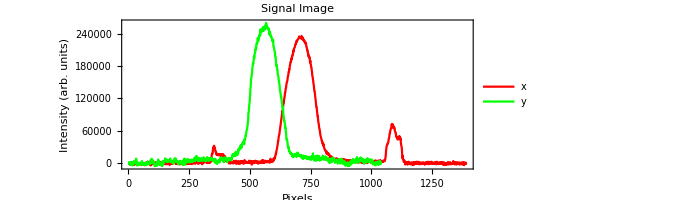
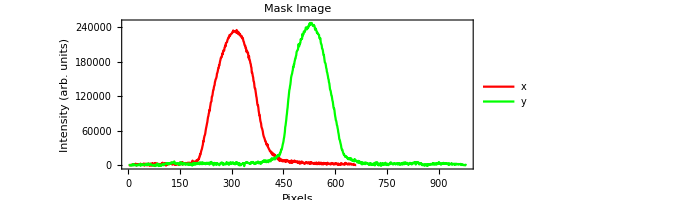
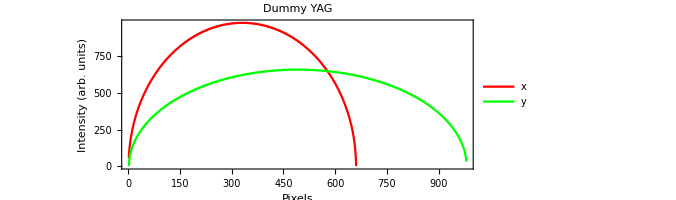

```mathematica
{ListPlot[SignalProj, PlotLabel ->  "Signal Image",Frame -> True, FrameLabel -> {"Pixels","Intensity (arb. units)"}, PlotLegends -> LineLegend[{Red,Green},{"x","y"}]],ListPlot[MaskProj, PlotLabel -> "Mask Image",Frame -> True, FrameLabel -> {"Pixels","Intensity (arb. units)"}, PlotLegends -> LineLegend[{Red,Green},{"x","y"}]],ListPlot[dummyYAGProj,PlotLabel -> "Dummy YAG",Frame -> True, FrameLabel -> {"Pixels","Intensity (arb. units)"}, PlotLegends -> LineLegend[{Red,Green},{"x","y"}]]}
```

## Scaled Mask Subtraction

Subtract a scaled mask of the image and choose the scaling to give a mean pixel valule of 0.

Here we subtract the dummy YAG, this is a matix containg an elipse, everyhting inside the elipse is equal to 1, everything outside the elipse is equal to zero.
It is exactly the same as the mask we applied to the image.

Now we subtract different multiples of the mask from the image, make a plot of the mean pixel value vs the multiple of mask we apply - in the plot below I show the result of subtracting multiples between -100 and 100 .

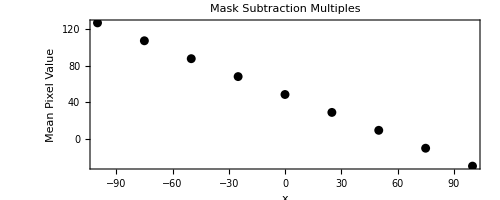

```mathematica
MaskSubData=Table[{x,Mean[Flatten[MaskImage-x dummyYAG]]},{x,-100,100,25}];
ListPlot[MaskSubData,Joined->False, PlotLabel -> "Mask Subtraction Multiples", Frame -> True, FrameLabel -> {"x", "Mean Pixel Value"}]
MaskSubFit = Fit[MaskSubData,{1,x},x];
MaskSubScaling= x/.Solve[MaskSubFit == 0,x][[1]];
```

Then do a linear fit to the plot and extract the x value (number we multiplied the mask by) that gives a y value of zero (mean pixel value of zero).

Next we can check this value by plotting two points, the mean of the image with no dummy mask subtracted at 0 and the mean of the image minus the dunny mask at 4095, these should give us the same answer as it is essentially the same plot.

```mathematica
MaskSubFit2=Fit[{{0,Mean[Flatten[MaskImage]]},{4095,Mean[Flatten[MaskImage-4095 dummyYAG]]}},{1,x},x];
MaskSubScaling2 = x/.Solve[MaskSubFit2==0,x][[1]];
```

Check they are the same (or at least similar)

```mathematica
If[MaskSubScaling == MaskSubScaling2,Print["Scaling Identical"],{MaskSubScaling,MaskSubScaling2}]
```

Scaling Identical

```mathematica
MaskScaleImage = MaskImage-MaskSubScaling dummyYAG;
MaskScaleBGProj=getXYProj2D[MaskScaleImage];
```

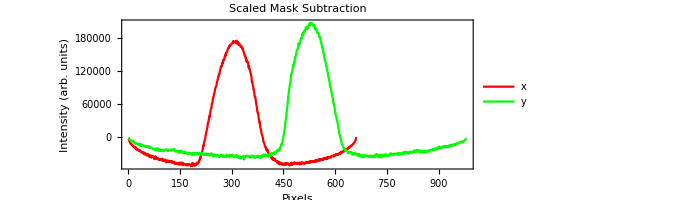

```mathematica
ListPlot[MaskScaleBGProj, PlotLabel -> "Scaled Mask Subtraction",Frame -> True, FrameLabel -> {"Pixels","Intensity (arb. units)"}, PlotLegends -> LineLegend[{Red,Green},{"x","y"}]]
```

## N Point Scaling

Now we try to scale the background to best match the first and last ten points.

This method assumes that the fist and last ten points in both the x and y directions are background and contain not beam or dark current signals.

First take the first and last ten points in x and y from the dummy YAG image.

```mathematica
mxS=dummyYAGProj⟦1⟧⟦1;;10⟧⟦All,2⟧;
mxE=dummyYAGProj⟦1⟧⟦-10;;-1⟧⟦All,2⟧;
myS=dummyYAGProj⟦2⟧⟦1;;10⟧⟦All,2⟧;
myE=dummyYAGProj⟦2⟧⟦-10;;-1⟧⟦All,2⟧;
dummyYAGpoints={mxS,mxE,myS,myE};
```

Then take the first and last x and y points from the image with the mask applied to it.

```mathematica
dxS=MaskProj⟦1⟧⟦1;;10⟧⟦All,2⟧;
dxE=MaskProj⟦1⟧⟦-10;;-1⟧⟦All,2⟧;
dyS=MaskProj⟦2⟧⟦1;;10⟧⟦All,2⟧;
dyE=MaskProj⟦2⟧⟦-10;;-1⟧⟦All,2⟧;
Maskpoints={dxS,dxE,dyS,dyE}
```

{{381.,241.,-293.,-403.,-471.,-241.,-318.,740.,380.,59.},{1377.,847.,70.,1139.,979.,648.,148.,108.,-59.,0.},{0.,178.,-139.,-103.,302.,-680.,-534.,-528.,104.,-541.},{531.,-114.,226.,-155.,-90.,451.,-352.,477.,165.,-142.}}

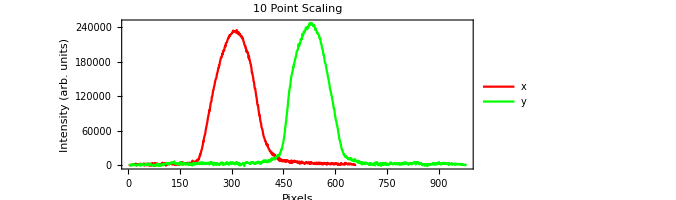

```mathematica
PointScaleImage2 = MaskImage - 0.2081655932478225 dummyYAG;
PointScaleBGProj2 = getXYProj2D[PointScaleImage2];
ListPlot[PointScaleBGProj2, PlotLabel -> "10 Point Scaling",Frame -> True, FrameLabel -> {"Pixels","Intensity (arb. units)"}, PlotLegends -> LineLegend[{Red,Green},{"x","y"}]]
```

Now find the best match and use that

Now we find a multiple of x that, when we multiply the points from the dummy YAG by x and subtract the points from the mask image, we take the x that gives the lowest value.
We do the first and last 10 points in the x and y direction (thus we have 4 values of x).

```mathematica
Table[NMinimize[RootMeanSquare[x dummyYAGpoints⟦i⟧-Maskpoints⟦i⟧],x],{i,1,4}]
```

{{390.699,{x→0.0737981}},{359.986,{x→4.15672}},{294.998,{x→-2.92151}},{292.694,{x→1.18118}}}

```mathematica
PointScale= Minimising[Table[NMinimize[RootMeanSquare[x dummyYAGpoints⟦i⟧-Maskpoints⟦i⟧],x],{i,1,4}]]
```

1.18118

We take this value of x and use it as our mask multiplier, subtracting x times the dummy mask from the image to get rid of the background

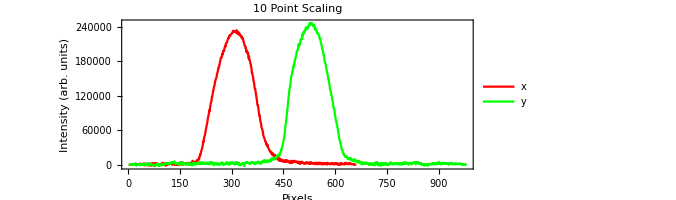

```mathematica
PointScaleImage = MaskImage - PointScale dummyYAG;
PointScaleBGProj = getXYProj2D[PointScaleImage];
ListPlot[PointScaleBGProj, PlotLabel -> "10 Point Scaling",Frame -> True, FrameLabel -> {"Pixels","Intensity (arb. units)"}, PlotLegends -> LineLegend[{Red,Green},{"x","y"}]]
```

## Comparison of Scaled Mask Subtraction & N Point Scaling

It is usefult to compare the two methods when doing the analysis by hand, so here we plot both projections to see which of the two methods reduces the image to the closest to a normal distribtion with the lowest amount of noise; as this will behave the best when we fit a Normal to analyse the image.

```mathematica
{ListPlot[MaskScaleBGProj, PlotLabel -> "Scaled Mask Subtraction",Frame -> True, FrameLabel -> {"Pixels","Intensity (arb. units)"}, PlotLegends -> LineLegend[{Red,Green},{"x","y"}]],ListPlot[PointScaleBGProj, PlotLabel -> "10 Point Scaling",Frame -> True, FrameLabel -> {"Pixels","Intensity (arb. units)"}, PlotLegends -> LineLegend[{Red,Green},{"x","y"}]]}
```

{-Graphics-,-Graphics-}

Although the two methods give very similar results, for most images it seems that the best method is the 10 point scaling as this gives the best representation of a Normal and has much flatter edges compared to the scaled mask subtraction, which can make the fitting process much easier.

To automate choosing the whcih of the methods gives the best projections use the BestBackground function.
This finds the variance of the off peak parts of the projections and returnthe name of the method that gives the lowest variance.

The image and projections of the method that gives the lowest variance are then used.

```mathematica
BBResult = BestBackground[MaskScaleBGProj,PointScaleBGProj];
If[BBResult[[1]] == "Scaled Mask", MaskBG = MaskScaleImage, MaskBG = PointScaleImage];

MaskBGProj = BBResult[[2]];
```

## Apply Projection Filters

Get the projections for the image minus the background

```mathematica
MaskBGProj = getXYProj2D[MaskBG];
ListPlot[MaskBGProj,Axes->True, PlotLabel -> "XY Projection",Frame -> True, FrameLabel -> {"Pixels","Intensity (arb. units)"}, PlotLegends -> LineLegend[{Red,Green},{"x","y"}]]
```

Apply a simple filter to the XY projections.
These just involve plotting the moving averages of the projections as explained in the report. This is done using the Mathematicas built in MovingAverage function.

### X - projection

```mathematica
ListPlot[{MovingAverage[MaskBGProj⟦1⟧,5],MovingAverage[MaskBGProj⟦1⟧,10],MovingAverage[MaskBGProj⟦1⟧,20]},Axes->True,Frame -> True,PlotLabel -> "X-Projection Filters", FrameLabel -> {"Pixels","Intensity (arb. units)"}, PlotLegends -> LineLegend[{Red,Green, Blue},{"5","10","20"}]]
```

### Y - projection

```mathematica
ListPlot[{MovingAverage[MaskBGProj⟦2⟧,5],MovingAverage[MaskBGProj⟦2⟧,10],MovingAverage[MaskBGProj⟦2⟧,20]},Axes->True,Frame -> True,PlotLabel -> "Y-Projection Filters", FrameLabel -> {"Pixels","Intensity (arb. units)"}, PlotLegends -> LineLegend[{Red,Green, Blue},{"5","10","20"}]]
```

3. Cutting The Image Down To Just The Beam Signal

## 1D Normal Fit Parameter Estimates

In this section we get the estimates for our 1D Normal fits from the projections.
The function get1DFitParamGuess calculates estimates using both the FWHM and Moments methods explained in the report and returns both sets of results, thus just pick out either the Moments (result 1) or the FWHM (result 2). 

get1DFitParamGuess is run on the x and y projections separately; it is also run on the filtered x and y projections to see what effect the filtering has on the image projections.

### Get Estimates Using X-Projection

Get the parameter estimates for the projection of the x projection of the image with the mask applied and minus the background.

```mathematica
xProjEstNoFilt = get1DFitParamGuess[MaskBGProj⟦1⟧];
xProjNoFiltMoments = Join[{Bg->#⟦1⟧,A->#⟦2⟧,μ->#⟦3⟧,σ->#⟦4⟧}&/@{xProjEstNoFilt[[1]]}][[1]];
xProjNoFiltFWHM = Join[{Bg->#⟦1⟧,A->#⟦2⟧,μ->#⟦3⟧,σ->#⟦4⟧}&/@{xProjEstNoFilt[[2]]}][[1]];
```

Then get the estimates for the filtered images.

```mathematica
xProjEstFilt5 = get1DFitParamGuess[MovingAverage[MaskBGProj⟦1⟧,5]];
xProjEstFilt10 =get1DFitParamGuess[MovingAverage[MaskBGProj⟦1⟧,10]];
xProjEstFilt20 =get1DFitParamGuess[MovingAverage[MaskBGProj⟦1⟧,20]];

xProjFilt5Moments = Join[{Bg->#⟦1⟧,A->#⟦2⟧,μ->#⟦3⟧,σ->#⟦4⟧}&/@{xProjEstFilt5[[1]]}][[1]];
xProjFilt5FWHM = Join[{Bg->#⟦1⟧,A->#⟦2⟧,μ->#⟦3⟧,σ->#⟦4⟧}&/@{xProjEstFilt5[[2]]}][[1]];
xProjFilt10Moments = Join[{Bg->#⟦1⟧,A->#⟦2⟧,μ->#⟦3⟧,σ->#⟦4⟧}&/@{xProjEstFilt10[[1]]}][[1]];
xProjFilt10FWHM = Join[{Bg->#⟦1⟧,A->#⟦2⟧,μ->#⟦3⟧,σ->#⟦4⟧}&/@{xProjEstFilt10[[2]]}][[1]];
xProjFilt20Moments = Join[{Bg->#⟦1⟧,A->#⟦2⟧,μ->#⟦3⟧,σ->#⟦4⟧}&/@{xProjEstFilt20[[1]]}][[1]];
xProjFilt20FWHM = Join[{Bg->#⟦1⟧,A->#⟦2⟧,μ->#⟦3⟧,σ->#⟦4⟧}&/@{xProjEstFilt20[[2]]}][[1]];
```

### Choosing The Best Filter For The Projection

Calculate which of the x filters is the most accurate, this is done by taking the filter that has the smallest proportional difference between the μ and σ values from the moments and FWHM methods used in get1DFitParamGuess as explained in the report; this is done in the BestFits function.

BestFits then returns a number based on the position of the best filter in the XEstimates list.

```mathematica
XEstimates = {xProjEstNoFilt,xProjEstFilt5,xProjEstFilt10,xProjEstFilt20};
XMoments = {xProjNoFiltMoments,xProjFilt5Moments,xProjFilt10Moments,xProjFilt20Moments};
XFWHM = {xProjNoFiltFWHM,xProjFilt5FWHM,xProjFilt10FWHM,xProjFilt20FWHM};
XBestFitPos = BestFits[XMoments,XFWHM];

xMomentsEst= XEstimates[[XBestFitPos]][[1]];
xFWHMEst = XEstimates[[XBestFitPos]][[2]];
xMomentsValues = XMoments[[XBestFitPos]];
xFWHMValues = XFWHM[[XBestFitPos]];

xProjEst = xFWHMEst;
xProjValues = xFWHMValues;
```

Use the FWHM estimates for the fit as these are generally the most accurate and use the projections with the filter that has been chosen from the BestFits function

```mathematica
XProjection = {MaskBGProj[[1]],MovingAverage[MaskBGProj⟦1⟧,5],MovingAverage[MaskBGProj⟦1⟧,10],MovingAverage[MaskBGProj⟦1⟧,20]}[[XBestFitPos]];
```

### Get Estimates Using Y-Projection

Get the parameter estimates for the projection of the y projection of the image with the mask applied and minus the background.

```mathematica
yProjEstNoFilt = get1DFitParamGuess[MaskBGProj⟦2⟧];
yProjNoFiltMoments = Join[{Bg->#⟦1⟧,A->#⟦2⟧,μ->#⟦3⟧,σ->#⟦4⟧}&/@{yProjEstNoFilt[[1]]}][[1]];
yProjNoFiltFWHM = Join[{Bg->#⟦1⟧,A->#⟦2⟧,μ->#⟦3⟧,σ->#⟦4⟧}&/@{yProjEstNoFilt[[2]]}][[1]];
```

Then get the estimates for the filtered images.

```mathematica
yProjEstFilt5 = get1DFitParamGuess[MovingAverage[MaskBGProj⟦2⟧,5]];
yProjEstFilt10 = get1DFitParamGuess[MovingAverage[MaskBGProj⟦2⟧,10]];
yProjEstFilt20 = get1DFitParamGuess[MovingAverage[MaskBGProj⟦2⟧,20]];

yProjFilt5Moments = Join[{Bg->#⟦1⟧,A->#⟦2⟧,μ->#⟦3⟧,σ->#⟦4⟧}&/@{yProjEstFilt5[[1]]}][[1]];
yProjFilt5FWHM = Join[{Bg->#⟦1⟧,A->#⟦2⟧,μ->#⟦3⟧,σ->#⟦4⟧}&/@{yProjEstFilt5[[2]]}][[1]];
yProjFilt10Moments = Join[{Bg->#⟦1⟧,A->#⟦2⟧,μ->#⟦3⟧,σ->#⟦4⟧}&/@{yProjEstFilt10[[1]]}][[1]];
yProjFilt10FWHM = Join[{Bg->#⟦1⟧,A->#⟦2⟧,μ->#⟦3⟧,σ->#⟦4⟧}&/@{yProjEstFilt10[[2]]}][[1]];
yProjFilt20Moments = Join[{Bg->#⟦1⟧,A->#⟦2⟧,μ->#⟦3⟧,σ->#⟦4⟧}&/@{yProjEstFilt20[[1]]}][[1]];
yProjFilt20FWHM = Join[{Bg->#⟦1⟧,A->#⟦2⟧,μ->#⟦3⟧,σ->#⟦4⟧}&/@{yProjEstFilt20[[2]]}][[1]];
```

### Choosing The Best Filter For The Projection

Calculate which of the y filters is the most accurate, this is done by taking the filter that has the smallest proportional difference between the μ and σ values from the moments and FWHM methods used in get1DFitParamGuess as explained in the report; this is done in the BestFits function.

BestFits then returns a number based on the position of the best filter in the XEstimates list.

```mathematica
YEstimates = {yProjEstNoFilt,yProjEstFilt5,yProjEstFilt10,yProjEstFilt20};
YMoments = {yProjNoFiltMoments,yProjFilt5Moments,yProjFilt10Moments,yProjFilt20Moments};
YFWHM = {yProjNoFiltFWHM,yProjFilt5FWHM,yProjFilt10FWHM,yProjFilt20FWHM};
YBestFitPos = BestFits[YMoments,YFWHM];

yMomentsEst= YEstimates[[YBestFitPos]][[1]];
yFWHMEst = YEstimates[[YBestFitPos]][[2]];
yMomentsValues = YMoments[[YBestFitPos]];
yFWHMValues = YFWHM[[YBestFitPos]];

yProjEst = yFWHMEst;
yProjValues = yFWHMValues;
```

Use the FWHM estimates for the fit as these are generally the most accurate and use the projections with the filter that has been chosen from the BestFits function

```mathematica
YProjection = {MaskBGProj⟦2⟧,MovingAverage[MaskBGProj⟦2⟧,2],MovingAverage[MaskBGProj⟦2⟧,10],MovingAverage[MaskBGProj⟦2⟧,20]}[[YBestFitPos]];
```

## Fit 1D Normal Distribution

Here fit the x and y projections with a 1D Normal using the fit1DN function, this just calles Mathemaicas NonLinearModelFit to fit the equation of a Gaussina given in the report, using the estimates calculated in the previous section.
Plot the fit using the plot1DFit function.

Note the fit1DN function is passed the projection and its corresponding estimates.

### Fit the X - Projection

```mathematica
xFit=fit1DN[XProjection,xProjEst];
xProjFitParam =Join[{Bg->#⟦1⟧,A->#⟦2⟧,μ->#⟦3⟧,σ->#⟦4⟧}&/@{xFit["BestFitParameters"]⟦All,2⟧}]⟦1⟧
plot1DFit[XProjection,xProjFitParam,"X-Projection 1D Normal Fit",{"Pixels","Intensity (arb. units)"}]
```

### Fit the Y - Projection

```mathematica
yFit=fit1DN[YProjection,yProjEst];
yProjFitParam = Join[{Bg->#⟦1⟧,A->#⟦2⟧,μ->#⟦3⟧,σ->#⟦4⟧}&/@{yFit["BestFitParameters"]⟦All,2⟧}]⟦1⟧
plot1DFit[YProjection,yProjFitParam,"Y-Projection 1D Normal Fit",{"Pixels","Intensity (arb. units)"}]
```

## Cutting The Image Down To Just The Beam Signal

After fitting the 1D Normal, use the values of μ and σ to cut the image.

### Check Residuals From 1D Normal Fit

Here we take the coeffieceint of determination (R^2) of the 1 D Normal fits, this is used to see if we have a ' good' fit.
    The coefficient of determination gives the proportion of the variance in the dependent variable that is predictable from the independant variable.
    It lies between 0 and 1, wil 1 meaning predictable without error and 0 meaning not predictable.
    This is returned from the NonLinearModelFit function.

```mathematica
XResiduals = xFit["RSquared"];
YResiduals = yFit["RSquared"];
```

### Choosing Between Fitting Parameters Or Estimates For The Cut

Here set the minimum value of R^2 that we can use for a fit. 
If the value of R^2 for a either the x or y projection fits is less than the limit then the estimates are used to cut the image.

The reason R^2 is used is to stop the program using fits that are completely wrong, suhc as if the peak is on wompletely the other side of the projection or the variance is way too big or too small.

The minimum R^2 value here is set to 0.4, while this may seem very low it is set to this becuase the low charge images produce projections with a alot of noise, especiallly on the off peak parts of the projections; thus when fitting to these projections the fit can turn out to be a very good fit, finding the mean position and peka width very well but can still fail the R^2 test due to the noise off peak projections being far from the background level.

We have found that setting the limit of R^2 to 0.4 still allows these noisy fits through but stops the cutting if the fits are completely off as explained earlier as these fits will have R^2 much less than 0.4.

```mathematica
If[XResiduals>0.4,XGoodFit = True,XGoodFit = False];
If[YResiduals>0.4,YGoodFit = True,YGoodFit = False];
```

```mathematica
If[XGoodFit==YGoodFit==True,GoodFit = True, GoodFit = False];
```

### Getting Cut Amount For Unfitted Data

.Set the number of sigma to cut at, by default this is set to three, however, this could be changed if need be. Can also change the amounts cut at using the fit or estimates separately.

```mathematica
If[XGoodFit == False,XCutAmount = 3,XCutAmount = 3];
If[YGoodFit == False, YCutAmount = 3, YCutAmount = 3];
```

### Applying Cut To Image

Apply the cut to the image using the cutFrom1DFit function with the parameters from either the fit or the estimates.
This returns the cut image (ImageCut) as well as the number of pixels cut in the x and y directions, which are added to a variable called CutParameters so that later on when we are correcting the values of the centre of the beam we can add on the number of pixels that were cut.

```mathematica
If[GoodFit == True,
Cutting= cutFrom1DFit[MaskBG,{μ/.xProjFitParam, σ/.xProjFitParam},{μ/.yProjFitParam,σ/.yProjFitParam},XCutAmount,YCutAmount];
ImageCut = Cutting[[1]];
CutParameters = {Cutting[[2]]};
CutMethods = {"Fit"};
]

If[GoodFit == False,
Cutting = cutFrom1DFit[MaskBG,{μ/.xProjValues, σ/.xProjValues},{μ/.yProjValues,σ/.yProjValues},XCutAmount,YCutAmount];
ImageCut = Cutting[[1]];
CutParameters = {Cutting[[2]]};
CutMethods = {"Estimates"};
]
```

Plot the original image and the cut image to compare, also display whcih method was used to cut the image.

```mathematica
CutMethods
ArrayPlot[MaskBG, PlotLabel -> "UnCut Image",Frame -> True, FrameLabel -> {"Y (Pixels)","X (Pixels)"}]
ArrayPlot[ImageCut, PlotLabel -> "Cut Image",Frame -> True, FrameLabel -> {"Y (Pixels)","X (Pixels)"}]
```

## Fit 1D Normal Distribution To Cut Image

The following steps are exactly the same as performed previously however this time they are performed on the new cut image data. All functions work in the Image Projections, Apply Projection Filter, 1D Normal Fit Parameter Estimates and Fit 1D Normal Distribution sections work in exactly the same way as before.

### Image Projections, Cut Image

```mathematica
CutProj = getXYProj2D[ImageCut];
```

```mathematica
ListPlot[CutProj, Axes -> True, PlotLabel -> "XY Projections ", Frame -> True, FrameLabel -> {"Pixels","Intensity (arb. units)"},PlotLegends -> LineLegend[{Red,Green},{"x","y"}]]
```

### Apply Projection Filters, Cut Image

Apply a simple filter to the XY projections

#### X - projection

```mathematica
ListPlot[{MovingAverage[CutProj⟦1⟧,5],MovingAverage[CutProj⟦1⟧,10],MovingAverage[CutProj⟦1⟧,20]},Axes->True, PlotLabel -> "Cut X-Projection Filters", Frame -> True, FrameLabel -> {"Pixels","Intensity (arb. units)"},PlotLegends -> LineLegend[{Red,Green,Blue},{"5","10","20"}]]
```

#### Y - projection

```mathematica
ListPlot[{MovingAverage[CutProj⟦2⟧,5],MovingAverage[CutProj⟦2⟧,10],MovingAverage[CutProj⟦2⟧,20]},Axes->True, PlotLabel -> "Cut Y-Projection Filters", Frame -> True, FrameLabel -> {"Pixels","Intensity (arb. units)"},PlotLegends -> LineLegend[{Red,Green,Blue},{"5","10","20"}]]
```

### 1D Normal Fit Parameter Estimates, Cut Image

#### X - Projection Estimates

```mathematica
CutxProjEstNoFilt = get1DFitParamGuess[CutProj[[1]]];
CutxProjNoFiltMoments = Join[{Bg->#⟦1⟧,A->#⟦2⟧,μ->#⟦3⟧,σ->#⟦4⟧}&/@{CutxProjEstNoFilt[[1]]}][[1]];
CutxProjNoFiltFWHM = Join[{Bg->#⟦1⟧,A->#⟦2⟧,μ->#⟦3⟧,σ->#⟦4⟧}&/@{CutxProjEstNoFilt[[2]]}][[1]];

CutxProjFiltEst5 = get1DFitParamGuess[MovingAverage[CutProj[[1]],5]];
CutxProjFiltEst10 = get1DFitParamGuess[MovingAverage[CutProj[[1]],10]];
CutxProjFiltEst20 = get1DFitParamGuess[MovingAverage[CutProj[[1]],20]];

CutxProjFilt5Moments = Join[{Bg->#⟦1⟧,A->#⟦2⟧,μ->#⟦3⟧,σ->#⟦4⟧}&/@{CutxProjFiltEst5[[1]]}][[1]];
CutxProjFilt5FWHM = Join[{Bg->#⟦1⟧,A->#⟦2⟧,μ->#⟦3⟧,σ->#⟦4⟧}&/@{CutxProjFiltEst5[[2]]}][[1]];
CutxProjFilt10Moments = Join[{Bg->#⟦1⟧,A->#⟦2⟧,μ->#⟦3⟧,σ->#⟦4⟧}&/@{CutxProjFiltEst10[[1]]}][[1]];
CutxProjFilt10FWHM = Join[{Bg->#⟦1⟧,A->#⟦2⟧,μ->#⟦3⟧,σ->#⟦4⟧}&/@{CutxProjFiltEst10[[2]]}][[1]];
CutxProjFilt20Moments = Join[{Bg->#⟦1⟧,A->#⟦2⟧,μ->#⟦3⟧,σ->#⟦4⟧}&/@{CutxProjFiltEst20[[1]]}][[1]];
CutxProjFilt20FWHM = Join[{Bg->#⟦1⟧,A->#⟦2⟧,μ->#⟦3⟧,σ->#⟦4⟧}&/@{CutxProjFiltEst20[[2]]}][[1]];
```

#### Choosing The Best Filter For The Projection

```mathematica
CutXEstimates = {CutxProjEstNoFilt,CutxProjFiltEst5,CutxProjFiltEst10,CutxProjFiltEst20};
CutXMoments = {CutxProjNoFiltMoments,CutxProjFilt5Moments,CutxProjFilt10Moments,CutxProjFilt20Moments};
CutXFWHM = {CutxProjNoFiltFWHM,CutxProjFilt5FWHM,CutxProjFilt10FWHM,CutxProjFilt20FWHM};
CutXBestFitPos = BestFits[CutXMoments,CutXFWHM];
BestFits[CutXMoments,CutXFWHM];

CutxMomentsEst= CutXEstimates[[CutXBestFitPos]][[1]];
CutxFWHMEst = CutXEstimates[[CutXBestFitPos]][[2]];
CutxMomentsValues = CutXMoments[[CutXBestFitPos]];
CutxFWHMValues = CutXFWHM[[CutXBestFitPos]];

CutxProjEst = CutxFWHMEst;
CutxProjValues = CutxFWHMValues;
```

Use corresponding projections

```mathematica
CutXProjection = {CutProj[[1]],MovingAverage[CutProj[[1]],5],MovingAverage[CutProj[[1]],10],MovingAverage[CutProj[[1]],20]}[[CutXBestFitPos]];
```

#### Y - Projection Estimates

```mathematica
CutyProjEstNoFilt = get1DFitParamGuess[CutProj[[2]]];
CutyProjNoFiltMoments = Join[{Bg->#⟦1⟧,A->#⟦2⟧,μ->#⟦3⟧,σ->#⟦4⟧}&/@{CutyProjEstNoFilt[[1]]}][[1]];
CutyProjNoFiltFWHM = Join[{Bg->#⟦1⟧,A->#⟦2⟧,μ->#⟦3⟧,σ->#⟦4⟧}&/@{CutyProjEstNoFilt[[2]]}][[1]];

CutyProjFiltEst5 = get1DFitParamGuess[MovingAverage[CutProj[[2]],5]];
CutyProjFiltEst10 = get1DFitParamGuess[MovingAverage[CutProj[[2]],10]];
CutyProjFiltEst20 = get1DFitParamGuess[MovingAverage[CutProj[[2]],20]];

CutyProjFilt5Moments = Join[{Bg->#⟦1⟧,A->#⟦2⟧,μ->#⟦3⟧,σ->#⟦4⟧}&/@{CutyProjFiltEst5[[1]]}][[1]];
CutyProjFilt5FWHM = Join[{Bg->#⟦1⟧,A->#⟦2⟧,μ->#⟦3⟧,σ->#⟦4⟧}&/@{CutyProjFiltEst5[[2]]}][[1]];
CutyProjFilt10Moments = Join[{Bg->#⟦1⟧,A->#⟦2⟧,μ->#⟦3⟧,σ->#⟦4⟧}&/@{CutyProjFiltEst10[[1]]}][[1]];
CutyProjFilt10FWHM = Join[{Bg->#⟦1⟧,A->#⟦2⟧,μ->#⟦3⟧,σ->#⟦4⟧}&/@{CutyProjFiltEst10[[2]]}][[1]];
CutyProjFilt20Moments = Join[{Bg->#⟦1⟧,A->#⟦2⟧,μ->#⟦3⟧,σ->#⟦4⟧}&/@{CutyProjFiltEst20[[1]]}][[1]];
CutyProjFilt20FWHM = Join[{Bg->#⟦1⟧,A->#⟦2⟧,μ->#⟦3⟧,σ->#⟦4⟧}&/@{CutyProjFiltEst20[[2]]}][[1]];
```

#### Choosing The Best Filter For The Projection

```mathematica
CutYEstimates = {CutyProjEstNoFilt,CutyProjFiltEst5,CutyProjFiltEst10,CutyProjFiltEst20};
CutYMoments = {CutyProjNoFiltMoments,CutyProjFilt5Moments,CutyProjFilt10Moments,CutyProjFilt20Moments};
CutYFWHM = {CutyProjNoFiltFWHM,CutyProjFilt5FWHM,CutyProjFilt10FWHM,CutyProjFilt20FWHM};
CutYBestFitPos = BestFits[CutYMoments,CutYFWHM];
BestFits[CutYMoments,CutYFWHM];

CutyMomentsEst= CutYEstimates[[CutYBestFitPos]][[1]];
CutyFWHMEst = CutYEstimates[[CutYBestFitPos]][[2]];
CutyMomentsValues = CutYMoments[[CutYBestFitPos]];
CutyFWHMValues = CutYFWHM[[CutYBestFitPos]];

CutyProjEst = CutyFWHMEst;
CutyProjValues = CutyFWHMValues;
```

```mathematica
CutYProjection = {CutProj[[2]],MovingAverage[CutProj[[2]],5],MovingAverage[CutProj[[2]],10],MovingAverage[CutProj[[2]],20]}[[CutYBestFitPos]];
```

### Fit 1D Normal Distribution, Cut Image

#### Fit the X - Projection

```mathematica
CutxFit=fit1DN[CutXProjection,CutxProjEst];
CutxProjFitParam = Join[{Bg->#⟦1⟧,A->#⟦2⟧,μ->#⟦3⟧,σ->#⟦4⟧}&/@{CutxFit["BestFitParameters"]⟦All,2⟧}]⟦1⟧
```

```mathematica
plot1DFit[CutXProjection,CutxProjFitParam,"Cut X-Projection 1D Normal Fit",{"Pixels","Intensity (arb. units)"}]
```

#### Fit the Y - Projection

```mathematica
CutyFit=fit1DN[CutYProjection,CutyProjEst];
CutyProjFitParam = Join[{Bg->#⟦1⟧,A->#⟦2⟧,μ->#⟦3⟧,σ->#⟦4⟧}&/@{CutyFit["BestFitParameters"]⟦All,2⟧}]⟦1⟧
```

```mathematica
plot1DFit[CutYProjection,CutyProjFitParam,"Cut Y-Projection 1D Normal Fit",{"Pixels","Intensity (arb. units)"}]
```

4. Fitting The BVN (BVN Method)

This section containts the BVN fitting as explained in the report, these fits will give the final answers for the beam centroid and variance.

The getBVNFit function fits the Bivariate Normal Distribution to the data using the estimates from the 1D Normal fit to the cut image.

The getBVNFit function also displays a countour plot of over the image, this can help check whether the beam centroid and variances seem correct.

```mathematica
BVNFit = getBVNFit[ImageCut,{A/.CutxProjFitParam,μ/.CutxProjFitParam,μ/.CutyProjFitParam,σ/.CutxProjFitParam,σ/.CutyProjFitParam},0]
```

5. Calculate Moments Of The Distribution (MLE Method)

The function getCovarianceMatrix directly calculates the covariance matrix from the cut image matrix using the moments as explained in the report.

```mathematica
MLEValues = Thread[{μx,μy,σ11,σ22,σ12}->getCovarianceMatrix[ImageCut]]
```

Therefore we end up with two sets of values from the analysis, one set from fitting the BVN and another from the MLE method.

6. Rescaling The Centroid Position

After the final analysis of the data (BVN and MLE) we must correct the values of μ. This is because when Mathematica displays the image matrices after the cuts and mask application, it only displays the non zero parts of the image.

For example if the first three columns in the image matrix were zero then Mathematica will plot the image with the origin in the fourth column - this is the cse for when the image is cut.
In the case of the masks, some columns/rows will contain both zero and non-zero values, this is due to the mask being an elipse, in this case Mathematica will still plot these columns but the corners of the image will have elements with zero values - this can be seen as smooth corners on the images with the mask applied.

The origin of the image is taken to be the bottom left coner of the original image (the one imported from the camera)

## Correcting for the image cutting

To correct for the cutting simply add on the number of pixels cut from the image between the origin and the beam centroid to the value of μ. This works due to Mathematica only plotting non-zero columns as mentioned previously.

The number of pixels cut in x and y are returned from the cutting function and stored in CutParameters, simply add on the correct ones to the values of μx and μy.

### Calculating the amount cut from x and y

```mathematica
XCutting = Table[CutParameters[[i,1]],{i,Length@CutParameters}];
YCutting = Table[CutParameters[[i,3]],{i,Length@CutParameters}];
```

### Plotting the contours

```mathematica
CutContourParameters = {Bg/.BVNFit[[1]], A/.BVNFit[[1]],(μx/.BVNFit[[1]]) + Total[XCutting],(μy/.BVNFit[[1]]) + Total[YCutting],σ11/.BVNFit[[1]],σ22/.BVNFit[[1]],σ12/.BVNFit[[1]]};
```

Overlay the BVN contours on the uncut image using the PlotContours function to check whether this has worked. Pass in the new, corrected parameters for the fit.

```mathematica
PlotContours[MaskBG, CutContourParameters]
```

## Correcting for the mask

To correct for the mask being applied simply add on the difference between the origin and the edge radius of the mask in the x and y direction, again this works due to the way Mathematica plots the images as explained previously. The values of the mask radius can be taken directly from the mask variable, again simply pick the correct ones, calculate the offsets and add them on to the values of μx and μy.

### Calculating the amount cut in x and y

```mathematica
maskYoffset = Mask[[4]] - Mask[[2]];
maskXoffset = Mask[[3]] - Mask[[1]];
```

This conditional statement is to acount for the radius of a mask being bigger than the size of the image, this could be the case in the mask needs to be larger than the image in one direction to fit to the shape of the screen. If this is the case then no offset is added on to the values of μ

```mathematica
If[maskYoffset < 0, maskYoffset = 0];
If[maskXoffset < 0, maskXoffset = 0];
```

### Plotting the contours

Again get the corrected parameters and plot the BVN contours to check whether the values seem correct, it is useful to plot the original image alongside for comparison, especially for low charge images.

```mathematica
MaskContourParameters = {Bg/.BVNFit[[1]], A/.BVNFit[[1]],(μx/.BVNFit[[1]]) + Total[XCutting] + maskXoffset,(μy/.BVNFit[[1]]) + Total[YCutting] + maskYoffset,σ11/.BVNFit[[1]],σ22/.BVNFit[[1]],σ12/.BVNFit[[1]]};
```

```mathematica
PlotContours[OrigImage, MaskContourParameters]
ArrayPlot[OrigImage,PlotLabel -> "Original Image", Frame -> True, FrameLabel -> {"Y (Pixels)","X (Pixels)"}]
```

## BVN & MLE Corrections

Finally apply all of the corrections to give final values for the BVN and MLE in pixels.

### BVN

```mathematica
BVNCorrections = {(μx/.BVNFit[[1]]) + Total[XCutting] + maskXoffset,(μy/.BVNFit[[1]]) + Total[YCutting] + maskYoffset,σ11/.BVNFit[[1]],σ22/.BVNFit[[1]],σ12/.BVNFit[[1]]};

BVN = Join [{μx->#⟦1⟧,μy->#⟦2⟧,σ11->#⟦3⟧,σ22->#⟦4⟧,σ12->#⟦5⟧} &/@{BVNCorrections}][[1]]
```

### MLE

```mathematica
MLECorrections = {(μx/.MLEValues) + Total[XCutting] + maskXoffset,(μy/.MLEValues) + Total[YCutting] + maskYoffset,σ11/.MLEValues,σ22/.MLEValues,σ12/.MLEValues};

MLE = Join [{μx->#⟦1⟧,μy->#⟦2⟧,σ11->#⟦3⟧,σ22->#⟦4⟧,σ12->#⟦5⟧} &/@{MLECorrections}][[1]]
```

7. Converting to millimetres

Finally convert the values from our BVN and MLE  from pixels into mm using the corrections for the respective screens.

The pixel to mm conversions are calculated as explained in the report, these can be found in the Pixel/mm Corrections section.

Note that the values of μ are given in pixels so are divided by the Pixel/mm conversion factor once; the values of σ are given in pixels^2 so are divided by the conversion factor squared.

## BVN

```mathematica
BVNmmCorrections = {((μx/.BVNFit[[1]]) + Total[XCutting] + maskXoffset)*(1/PixelMM),((μy/.BVNFit[[1]]) + Total[YCutting] + maskYoffset)*(1/PixelMM),(σ11/.BVNFit[[1]])*(1/(PixelMM^2)),(σ22/.BVNFit[[1]])*(1/(PixelMM^2)),(σ12/.BVNFit[[1]])*(1/(PixelMM^2))};
```

```mathematica
FinalBVN = Join [{μx->#⟦1⟧,μy->#⟦2⟧,σ11->#⟦3⟧,σ22->#⟦4⟧,σ12->#⟦5⟧} &/@{BVNmmCorrections}][[1]]
```

## MLE

```mathematica
MLEmmCorrections = {((μx/.MLEValues) + Total[XCutting] + maskXoffset)*(1/PixelMM),((μy/.MLEValues) + Total[YCutting] + maskYoffset)*(1/PixelMM),(σ11/.MLEValues)*(1/(PixelMM^2)),(σ22/.MLEValues)*(1/(PixelMM^2)),(σ12/.MLEValues)*(1/(PixelMM^2))};
```

```mathematica
FinalMLE = Join [{μx->#⟦1⟧,μy->#⟦2⟧,σ11->#⟦3⟧,σ22->#⟦4⟧,σ12->#⟦5⟧} &/@{MLEmmCorrections}][[1]]
```

## Final Values

Finally we have the BVN and MLE sets of values in mm.

```mathematica
{"BVN",FinalBVN}
{"MLE",FinalMLE}
```

## Image Analysis Function

This section is a function contating all of the code shown above, it does not print all of teh plots to the screen as the step by step code in the previous section, it just returns the final values from the BVN and MLE methods as well as the contour plots over the original and cut images, the original image itself, which background subtraction method was used and whether the image was cut using the fits or the estimates.

## Function Declaration

```mathematica
MachineImageAnalysis[ImportDirectory_,ImageFile_,BackFile_:"None",Screen_]:=
(
(*Importing Data*)
(*Import the image with beam and backgroud image .raw files*)
SetDirectory[ImportDirectory];
ImageFilename=FileNames[ImageFile];
OrigImage=fpr[importVELAraw[ImageFilename⟦1⟧],1392];
If[BackFile ≠ "None",
(*Subtract the background image from the original if it exists*)
backgroundFilename = FileNames[BackFile];
backImage = fpr[importVELAraw[backgroundFilename⟦1⟧], 1392];
SignalImage= OrigImage-backImage;,
(*Else just use the image file with no background subtracted*)
SignalImage= OrigImage;];

(*Set which mask is to be used and the pixel to mm conversion factor, these are based on which screen the image is taken from*)
If[Screen ==1,Mask = yag1Mask;dummyYAG = dummyYAG1;PixelMM = YAG1PM;];
If[Screen==2,Mask= yag2Mask;dummyYAG = dummyYAG2;PixelMM = YAG2PM;];
If[Screen==3,Mask= yag3Mask;dummyYAG = dummyYAG3;PixelMM = YAG3PM;];
(*Apply the mask to the image array*)
MaskImage= applyMask[SignalImage,Mask];

(*Background Subtraction*)

(*Get the projections of the original image, image afer the mask has been applied and projections of the mask itself (dummyYAG)*)
SignalProj=getXYProj2D[SignalImage];
MaskProj=getXYProj2D[MaskImage];
dummyYAGProj=getXYProj2D[dummyYAG];

(*Scaled Mask Subtraction*)
(*Subtract different multiples of the mask from the image, ranging from -100 to 100 in steps of 25, and calculate the mean pixel value in each case*)
MaskSubData=Table[{x,Mean[Flatten[MaskImage-x dummyYAG]]},{x,-100,100,25}];
(*Fit to the linearly to x versus mean pixel value and solve for x when mean pixel value equals 0*)
MaskSubFit = Fit[MaskSubData,{1,x},x];
MaskSubScaling= x/.Solve[MaskSubFit == 0,x][[1]];
(*Using the x that gives the mean pixel value of 0, subtract x times the mask from the image*)
MaskScaleImage = MaskImage-MaskSubScaling dummyYAG;
(*Get the projections of the image after the Scaled Mask Subtraction*)
MaskScaleBGProj=getXYProj2D[MaskScaleImage];

(*10 Point Scaling*)
(*Take the first and last ten points in x and y from the projections of the mask*)
mxS=dummyYAGProj⟦1⟧⟦1;;10⟧⟦All,2⟧;
mxE=dummyYAGProj⟦1⟧⟦-10;;-1⟧⟦All,2⟧;
myS=dummyYAGProj⟦2⟧⟦1;;10⟧⟦All,2⟧;
mxE=dummyYAGProj⟦2⟧⟦-10;;-1⟧⟦All,2⟧;
dummyYAGpoints={mxS,mxE,myS,mxE};
(*Take the first and last ten points in x and y from the projections of the image after the mask has been applied*)
dxS=MaskProj⟦1⟧⟦1;;10⟧⟦All,2⟧;
dxE=MaskProj⟦1⟧⟦-10;;-1⟧⟦All,2⟧;
dyS=MaskProj⟦2⟧⟦1;;10⟧⟦All,2⟧;
dyE=MaskProj⟦2⟧⟦-10;;-1⟧⟦All,2⟧;
Maskpoints={dxS,dxE,dyS,dyE};
(*Find the multiple of x that, when we multiply the points from the dummy YAG by x and subtract the points from the image, we tke the x that gives the lowest value. We do the first and last 10 points in the x and y direction (thus we have 4 values of x). *)
Table[NMinimize[RootMeanSquare[x dummyYAGpoints⟦i⟧-Maskpoints⟦i⟧],x],{i,1,4}];
PointScale= Minimising[Table[NMinimize[RootMeanSquare[x dummyYAGpoints⟦i⟧-Maskpoints⟦i⟧],x],{i,1,4}]];
(*Subtract the chosen multiple of x times the mask away from the image after the mask has been applied*)
PointScaleImage = MaskImage - PointScale dummyYAG;
(*Get the projection of image after the N Point Scaling background subtraction*)
PointScaleBGProj = getXYProj2D[PointScaleImage];

(*Comparing The Two Methods*)
(*Compare the two background subtraction methods to see which is the best to use, this is further explained in the bestBackground function declaration section at the top of the notebook*)
BBResult = BestBackground[MaskScaleBGProj,PointScaleBGProj];
If[BBResult[[1]] == "Scaled Mask", MaskBG = MaskScaleImage, MaskBG = PointScaleImage];

(*XY Projections*)
(*Use the projections from the 'best' background subtraction method from this point on in the program*)
MaskBGProj = BBResult[[2]];

(*Fitting Parameter Estimates*)
(*Estimate fitting parametesr for a 1D Normal fit to the projections. This section calls the functions that use the FWHM and Moments methods to estimate the fitting parameters*)
(*X*)
xProjEstNoFilt = get1DFitParamGuess[MaskBGProj⟦1⟧];
xProjNoFiltMoments = Join[{Bg->#⟦1⟧,A->#⟦2⟧,μ->#⟦3⟧,σ->#⟦4⟧}&/@{xProjEstNoFilt[[1]]}][[1]];
xProjNoFiltFWHM = Join[{Bg->#⟦1⟧,A->#⟦2⟧,μ->#⟦3⟧,σ->#⟦4⟧}&/@{xProjEstNoFilt[[2]]}][[1]];

xProjEstFilt5 = get1DFitParamGuess[MovingAverage[MaskBGProj⟦1⟧,5]];
xProjEstFilt10 =get1DFitParamGuess[MovingAverage[MaskBGProj⟦1⟧,10]];
xProjEstFilt20 =get1DFitParamGuess[MovingAverage[MaskBGProj⟦1⟧,20]];

xProjFilt5Moments = Join[{Bg->#⟦1⟧,A->#⟦2⟧,μ->#⟦3⟧,σ->#⟦4⟧}&/@{xProjEstFilt5[[1]]}][[1]];
xProjFilt5FWHM = Join[{Bg->#⟦1⟧,A->#⟦2⟧,μ->#⟦3⟧,σ->#⟦4⟧}&/@{xProjEstFilt5[[2]]}][[1]];
xProjFilt10Moments = Join[{Bg->#⟦1⟧,A->#⟦2⟧,μ->#⟦3⟧,σ->#⟦4⟧}&/@{xProjEstFilt10[[1]]}][[1]];
xProjFilt10FWHM = Join[{Bg->#⟦1⟧,A->#⟦2⟧,μ->#⟦3⟧,σ->#⟦4⟧}&/@{xProjEstFilt10[[2]]}][[1]];
xProjFilt20Moments = Join[{Bg->#⟦1⟧,A->#⟦2⟧,μ->#⟦3⟧,σ->#⟦4⟧}&/@{xProjEstFilt20[[1]]}][[1]];
xProjFilt20FWHM = Join[{Bg->#⟦1⟧,A->#⟦2⟧,μ->#⟦3⟧,σ->#⟦4⟧}&/@{xProjEstFilt20[[2]]}][[1]];

XEstimates = {xProjEstNoFilt,xProjEstFilt5,xProjEstFilt10,xProjEstFilt20};
XMoments = {xProjNoFiltMoments,xProjFilt5Moments,xProjFilt10Moments,xProjFilt20Moments};
XFWHM = {xProjNoFiltFWHM,xProjFilt5FWHM,xProjFilt10FWHM,xProjFilt20FWHM};
XBestFitPos = BestFits[XMoments,XFWHM];

xMomentsEst= XEstimates[[XBestFitPos]][[1]];
xFWHMEst = XEstimates[[XBestFitPos]][[2]];
xMomentsValues = XMoments[[XBestFitPos]];
xFWHMValues = XFWHM[[XBestFitPos]];

xProjEst = xFWHMEst;
xProjValues = xFWHMValues;

XProjection = {MaskBGProj[[1]],MovingAverage[MaskBGProj⟦1⟧,5],MovingAverage[MaskBGProj⟦1⟧,10],MovingAverage[MaskBGProj⟦1⟧,20]}[[XBestFitPos]];

(*Y*)
yProjEstNoFilt = get1DFitParamGuess[MaskBGProj⟦2⟧];
yProjNoFiltMoments = Join[{Bg->#⟦1⟧,A->#⟦2⟧,μ->#⟦3⟧,σ->#⟦4⟧}&/@{yProjEstNoFilt[[1]]}][[1]];
yProjNoFiltFWHM = Join[{Bg->#⟦1⟧,A->#⟦2⟧,μ->#⟦3⟧,σ->#⟦4⟧}&/@{yProjEstNoFilt[[2]]}][[1]];

yProjEstFilt5 = get1DFitParamGuess[MovingAverage[MaskBGProj⟦2⟧,5]];
yProjEstFilt10 = get1DFitParamGuess[MovingAverage[MaskBGProj⟦2⟧,10]];
yProjEstFilt20 = get1DFitParamGuess[MovingAverage[MaskBGProj⟦2⟧,20]];

yProjFilt5Moments = Join[{Bg->#⟦1⟧,A->#⟦2⟧,μ->#⟦3⟧,σ->#⟦4⟧}&/@{yProjEstFilt5[[1]]}][[1]];
yProjFilt5FWHM = Join[{Bg->#⟦1⟧,A->#⟦2⟧,μ->#⟦3⟧,σ->#⟦4⟧}&/@{yProjEstFilt5[[2]]}][[1]];
yProjFilt10Moments = Join[{Bg->#⟦1⟧,A->#⟦2⟧,μ->#⟦3⟧,σ->#⟦4⟧}&/@{yProjEstFilt10[[1]]}][[1]];
yProjFilt10FWHM = Join[{Bg->#⟦1⟧,A->#⟦2⟧,μ->#⟦3⟧,σ->#⟦4⟧}&/@{yProjEstFilt10[[2]]}][[1]];
yProjFilt20Moments = Join[{Bg->#⟦1⟧,A->#⟦2⟧,μ->#⟦3⟧,σ->#⟦4⟧}&/@{yProjEstFilt20[[1]]}][[1]];
yProjFilt20FWHM = Join[{Bg->#⟦1⟧,A->#⟦2⟧,μ->#⟦3⟧,σ->#⟦4⟧}&/@{yProjEstFilt20[[2]]}][[1]];

YEstimates = {yProjEstNoFilt,yProjEstFilt5,yProjEstFilt10,yProjEstFilt20};
YMoments = {yProjNoFiltMoments,yProjFilt5Moments,yProjFilt10Moments,yProjFilt20Moments};
YFWHM = {yProjNoFiltFWHM,yProjFilt5FWHM,yProjFilt10FWHM,yProjFilt20FWHM};
YBestFitPos = BestFits[YMoments,YFWHM];

yMomentsEst= YEstimates[[YBestFitPos]][[1]];
yFWHMEst = YEstimates[[YBestFitPos]][[2]];
yMomentsValues = YMoments[[YBestFitPos]];
yFWHMValues = YFWHM[[YBestFitPos]];

yProjEst = yFWHMEst;
yProjValues = yFWHMValues;

YProjection = {MaskBGProj⟦2⟧,MovingAverage[MaskBGProj⟦2⟧,2],MovingAverage[MaskBGProj⟦2⟧,10],MovingAverage[MaskBGProj⟦2⟧,20]}[[YBestFitPos]];

(*Fitting 1D Gaussian*)

(*X*)
xFit=fit1DN[XProjection,xProjEst];
xProjFitParam = Join[{Bg->#⟦1⟧,A->#⟦2⟧,μ->#⟦3⟧,σ->#⟦4⟧}&/@{xFit["BestFitParameters"]⟦All,2⟧}]⟦1⟧;

(*Y*)
yFit=fit1DN[YProjection,yProjEst];
yProjFitParam = Join[{Bg->#⟦1⟧,A->#⟦2⟧,μ->#⟦3⟧,σ->#⟦4⟧}&/@{yFit["BestFitParameters"]⟦All,2⟧}]⟦1⟧;

(*Cutting The Image*)
XResiduals = xFit["RSquared"];
YResiduals = yFit["RSquared"];

If[XResiduals>0.4,XGoodFit = True,XGoodFit = False];
If[YResiduals>0.4,YGoodFit = True,YGoodFit = False];
If[XGoodFit==YGoodFit==True,GoodFit = True, GoodFit = False];

If[XGoodFit == False,XCutAmount = 3,XCutAmount = 3];
If[YGoodFit == False, YCutAmount = 3, YCutAmount = 3];

If[GoodFit == True,
Cutting= cutFrom1DFit[MaskBG,{μ/.xProjFitParam, σ/.xProjFitParam},{μ/.yProjFitParam,σ/.yProjFitParam},XCutAmount,YCutAmount];
ImageCut = Cutting[[1]];
CutParameters = {Cutting[[2]]};
CutMethods = {"Fit"};
]

If[GoodFit == False,
Cutting = cutFrom1DFit[MaskBG,{μ/.xProjValues, σ/.xProjValues},{μ/.yProjValues,σ/.yProjValues},XCutAmount,YCutAmount];
ImageCut = Cutting[[1]];
CutParameters = {Cutting[[2]]};
CutMethods = {"Estimates"};
];


(*XY Projections Cut Image*)
CutProj = getXYProj2D[ImageCut];

(*Parameter Estimates, Cut Image*)
(*X*)

CutxProjEstNoFilt = get1DFitParamGuess[CutProj[[1]]];
CutxProjNoFiltMoments = Join[{Bg->#⟦1⟧,A->#⟦2⟧,μ->#⟦3⟧,σ->#⟦4⟧}&/@{CutxProjEstNoFilt[[1]]}][[1]];
CutxProjNoFiltFWHM = Join[{Bg->#⟦1⟧,A->#⟦2⟧,μ->#⟦3⟧,σ->#⟦4⟧}&/@{CutxProjEstNoFilt[[2]]}][[1]];

CutxProjFiltEst5 = get1DFitParamGuess[MovingAverage[CutProj[[1]],5]];
CutxProjFiltEst10 = get1DFitParamGuess[MovingAverage[CutProj[[1]],10]];
CutxProjFiltEst20 = get1DFitParamGuess[MovingAverage[CutProj[[1]],20]];

CutxProjFilt5Moments = Join[{Bg->#⟦1⟧,A->#⟦2⟧,μ->#⟦3⟧,σ->#⟦4⟧}&/@{CutxProjFiltEst5[[1]]}][[1]];
CutxProjFilt5FWHM = Join[{Bg->#⟦1⟧,A->#⟦2⟧,μ->#⟦3⟧,σ->#⟦4⟧}&/@{CutxProjFiltEst5[[2]]}][[1]];
CutxProjFilt10Moments = Join[{Bg->#⟦1⟧,A->#⟦2⟧,μ->#⟦3⟧,σ->#⟦4⟧}&/@{CutxProjFiltEst10[[1]]}][[1]];
CutxProjFilt10FWHM = Join[{Bg->#⟦1⟧,A->#⟦2⟧,μ->#⟦3⟧,σ->#⟦4⟧}&/@{CutxProjFiltEst10[[2]]}][[1]];
CutxProjFilt20Moments = Join[{Bg->#⟦1⟧,A->#⟦2⟧,μ->#⟦3⟧,σ->#⟦4⟧}&/@{CutxProjFiltEst20[[1]]}][[1]];
CutxProjFilt20FWHM = Join[{Bg->#⟦1⟧,A->#⟦2⟧,μ->#⟦3⟧,σ->#⟦4⟧}&/@{CutxProjFiltEst20[[2]]}][[1]];

CutXEstimates = {CutxProjEstNoFilt,CutxProjFiltEst5,CutxProjFiltEst10,CutxProjFiltEst20};
CutXMoments = {CutxProjNoFiltMoments,CutxProjFilt5Moments,CutxProjFilt10Moments,CutxProjFilt20Moments};
CutXFWHM = {CutxProjNoFiltFWHM,CutxProjFilt5FWHM,CutxProjFilt10FWHM,CutxProjFilt20FWHM};
CutXBestFitPos = BestFits[CutXMoments,CutXFWHM];

CutxMomentsEst= CutXEstimates[[CutXBestFitPos]][[1]];
CutxFWHMEst = CutXEstimates[[CutXBestFitPos]][[2]];
CutxMomentsValues = CutXMoments[[CutXBestFitPos]];
CutxFWHMValues = CutXFWHM[[CutXBestFitPos]];

CutxProjEst = CutxFWHMEst;
CutxProjValues = CutxFWHMValues;

CutXProjection = {CutProj[[1]],MovingAverage[CutProj[[1]],5],MovingAverage[CutProj[[1]],10],MovingAverage[CutProj[[1]],20]}[[CutXBestFitPos]];

(*Y*)
CutyProjEstNoFilt = get1DFitParamGuess[CutProj[[2]]];
CutyProjNoFiltMoments = Join[{Bg->#⟦1⟧,A->#⟦2⟧,μ->#⟦3⟧,σ->#⟦4⟧}&/@{CutyProjEstNoFilt[[1]]}][[1]];
CutyProjNoFiltFWHM = Join[{Bg->#⟦1⟧,A->#⟦2⟧,μ->#⟦3⟧,σ->#⟦4⟧}&/@{CutyProjEstNoFilt[[2]]}][[1]];

CutyProjFiltEst5 = get1DFitParamGuess[MovingAverage[CutProj[[2]],5]];
CutyProjFiltEst10 = get1DFitParamGuess[MovingAverage[CutProj[[2]],10]];
CutyProjFiltEst20 = get1DFitParamGuess[MovingAverage[CutProj[[2]],20]];

CutyProjFilt5Moments = Join[{Bg->#⟦1⟧,A->#⟦2⟧,μ->#⟦3⟧,σ->#⟦4⟧}&/@{CutyProjFiltEst5[[1]]}][[1]];
CutyProjFilt5FWHM = Join[{Bg->#⟦1⟧,A->#⟦2⟧,μ->#⟦3⟧,σ->#⟦4⟧}&/@{CutyProjFiltEst5[[2]]}][[1]];
CutyProjFilt10Moments = Join[{Bg->#⟦1⟧,A->#⟦2⟧,μ->#⟦3⟧,σ->#⟦4⟧}&/@{CutyProjFiltEst10[[1]]}][[1]];
CutyProjFilt10FWHM = Join[{Bg->#⟦1⟧,A->#⟦2⟧,μ->#⟦3⟧,σ->#⟦4⟧}&/@{CutyProjFiltEst10[[2]]}][[1]];
CutyProjFilt20Moments = Join[{Bg->#⟦1⟧,A->#⟦2⟧,μ->#⟦3⟧,σ->#⟦4⟧}&/@{CutyProjFiltEst20[[1]]}][[1]];
CutyProjFilt20FWHM = Join[{Bg->#⟦1⟧,A->#⟦2⟧,μ->#⟦3⟧,σ->#⟦4⟧}&/@{CutyProjFiltEst20[[2]]}][[1]];

CutYEstimates = {CutyProjEstNoFilt,CutyProjFiltEst5,CutyProjFiltEst10,CutyProjFiltEst20};
CutYMoments = {CutyProjNoFiltMoments,CutyProjFilt5Moments,CutyProjFilt10Moments,CutyProjFilt20Moments};
CutYFWHM = {CutyProjNoFiltFWHM,CutyProjFilt5FWHM,CutyProjFilt10FWHM,CutyProjFilt20FWHM};
CutYBestFitPos = BestFits[CutYMoments,CutYFWHM];

CutyMomentsEst= CutYEstimates[[CutYBestFitPos]][[1]];
CutyFWHMEst = CutYEstimates[[CutYBestFitPos]][[2]];
CutyMomentsValues = CutYMoments[[CutYBestFitPos]];
CutyFWHMValues = CutYFWHM[[CutYBestFitPos]];

CutyProjEst = CutyFWHMEst;
CutyProjValues = CutyFWHMValues;

CutYProjection = {CutProj[[2]],MovingAverage[CutProj[[2]],5],MovingAverage[CutProj[[2]],10],MovingAverage[CutProj[[2]],20]}[[CutYBestFitPos]];

(*Fitting 1D Gaussian, Cut Image*)
(*X*)
CutxFit=fit1DN[CutXProjection,CutxProjEst];
CutxProjFitParam = Join[{Bg->#⟦1⟧,A->#⟦2⟧,μ->#⟦3⟧,σ->#⟦4⟧}&/@{CutxFit["BestFitParameters"]⟦All,2⟧}]⟦1⟧;
(*Y*)
CutyFit=fit1DN[CutYProjection,CutyProjEst];
CutyProjFitParam = Join[{Bg->#⟦1⟧,A->#⟦2⟧,μ->#⟦3⟧,σ->#⟦4⟧}&/@{CutyFit["BestFitParameters"]⟦All,2⟧}]⟦1⟧;

(*BVN Fit*)
BVNFit = getBVNFitFunc[ImageCut,{A/.CutxProjFitParam,μ/.CutxProjFitParam,μ/.CutyProjFitParam,σ/.CutxProjFitParam,σ/.CutyProjFitParam}];


CutContourParameters = {Bg/.BVNFit[[1]], A/.BVNFit[[1]],(μx/.BVNFit[[1]]) ,(μy/.BVNFit[[1]]),σ11/.BVNFit[[1]],σ22/.BVNFit[[1]],σ12/.BVNFit[[1]]};

CutContourPlot = PlotContours[ImageCut,CutContourParameters," Cut Contour Plot"];

(*MLE*)
MLEValues = Thread[{μxC,μyC,σ11,σ22,σ12}->getCovarianceMatrix[ImageCut]];

(*Correcting μ*)

(*Image Cutting*)
XCutting = Table[CutParameters[[i,1]],{i,Length@CutParameters}];
YCutting = Table[CutParameters[[i,3]],{i,Length@CutParameters}];

(*Mask Offset*)
maskYoffset = Mask[[4]] - Mask[[2]];
maskXoffset = Mask[[3]] - Mask[[1]];

If[maskYoffset < 0, maskYoffset = 0];
If[maskXoffset < 0, maskXoffset = 0]; 

ContourParameters = {Bg/.BVNFit[[1]], A/.BVNFit[[1]],(μx/.BVNFit[[1]]) + Total[XCutting] + maskXoffset,(μy/.BVNFit[[1]]) + Total[YCutting] + maskYoffset,σ11/.BVNFit[[1]],σ22/.BVNFit[[1]],σ12/.BVNFit[[1]]};

ContourImage = PlotContours[OrigImage,ContourParameters," Contour Plot"];
OrigImagePlot = Show[ArrayPlot[OrigImage,PlotLabel ->  " Original Image",Frame -> True, FrameLabel -> {"y (Pixels)","x (Pixels)"}]];

(*BVN & Covariance Corrections*)
BVNCorrections = {(μx/.BVNFit[[1]]) + Total[XCutting] + maskXoffset,(μy/.BVNFit[[1]]) + Total[YCutting] + maskYoffset,σ11/.BVNFit[[1]],σ22/.BVNFit[[1]],σ12/.BVNFit[[1]]};

BVNParameters = Join [{μx->#⟦1⟧,μy->#⟦2⟧,σ11->#⟦3⟧,σ22->#⟦4⟧,σ12->#⟦5⟧} &/@{BVNCorrections}][[1]];

MLECorrections = {(μxC/.MLEValues) + Total[XCutting] + maskXoffset,(μyC/.MLEValues) + Total[YCutting] + maskYoffset,σ11/.MLEValues,σ22/.MLEValues,σ12/.MLEValues};

MLEParameters = Join [{μx->#⟦1⟧,μy->#⟦2⟧,σ11->#⟦3⟧,σ22->#⟦4⟧,σ12->#⟦5⟧} &/@{MLECorrections}][[1]];

(*Converting to mm*)
BVNmmCorrections = {((μx/.BVNFit[[1]]) + Total[XCutting] + maskXoffset)*(1/PixelMM),((μy/.BVNFit[[1]]) + Total[YCutting] + maskYoffset)*(1/PixelMM),(σ11/.BVNFit[[1]])*(1/(PixelMM^2)),(σ22/.BVNFit[[1]])*(1/(PixelMM^2)),(σ12/.BVNFit[[1]])*(1/(PixelMM^2))};

FinalBVN = Join [{μx->#⟦1⟧,μy->#⟦2⟧,σ11->#⟦3⟧,σ22->#⟦4⟧,σ12->#⟦5⟧} &/@{BVNmmCorrections}][[1]];

MLEmmCorrections = {((μxC/.MLEValues) + Total[XCutting] + maskXoffset)*(1/PixelMM),((μyC/.MLEValues) + Total[YCutting] + maskYoffset)*(1/PixelMM),(σ11/.MLEValues)*(1/(PixelMM^2)),(σ22/.MLEValues)*(1/(PixelMM^2)),(σ12/.MLEValues)*(1/(PixelMM^2))};

FinalMLE = Join [{μx->#⟦1⟧,μy->#⟦2⟧,σ11->#⟦3⟧,σ22->#⟦4⟧,σ12->#⟦5⟧} &/@{MLEmmCorrections}][[1]];

FinalValues = {{"BVN",FinalBVN},{"MLE",FinalMLE},{CutMethods}, {BBResult[[1]]},{ContourImage},{OrigImagePlot},{CutContourPlot}}
)
```

## Run Function

```mathematica
MachineImageAnalysis["\\\\fed.cclrc.ac.uk\\org\\NLab\\ASTeC\\Projects\\VELA\\Work\\2015\\10\\22\\2015-10-22 Model Validation Data\\sol155\\bsol0\\YAG-01\\VC1\\50pc","2019 YAG-01 20151022201952701.raw","2020 YAG-01 20151022202037633.raw",1]
```

# 2019 cross - checking python script for controls group on noisey image

```mathematica
SetDirectory["\\\\fed.cclrc.ac.uk\\Org\\NLab\\ASTeC\\Projects\\VELA\\Work\\2019\\03\\04\\10pC degaussing, sol -125.0"];
OrigImage=Import["S02-CAM-03_2019-3-4_17-49-55_10images.hdf5","/Capture000001"];
backImage = Import["S02-CAM-03_2019-3-4_17-50-13_1images.hdf5","/Capture000001"];
SignalImage= beamimage-backimage;
```

```mathematica
Mask={400,750,1000,900};
```

```mathematica
MaskImage= applyMask[OrigImage,Mask];
```

```mathematica
OrigImageCut=crop[OrigImage,{1000-400,1000+400-1,900-750,900+750-1}];
```

```mathematica
mask0=applyMask[ConstantArray[1,{Length@OrigImageCut,Length@OrigImageCut⟦1⟧}],{400,750,Floor@((Length@OrigImageCut⟦1⟧)/2),Floor@((Length@OrigImageCut)/2)}];
```

```mathematica
{MatrixPlot[OrigImageCut],MatrixPlot[mask0],MatrixPlot[OrigImageCut mask0]}
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
originalProj=getXYProj2D[OrigImageCut];
MaskProj=getXYProj2D[mask0];
dataproj=getXYProj2D[OrigImageCut mask0];
```

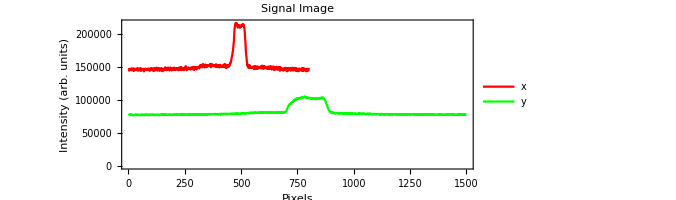
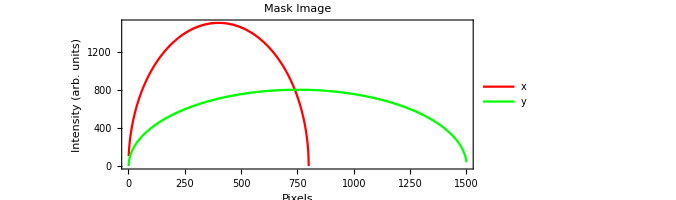
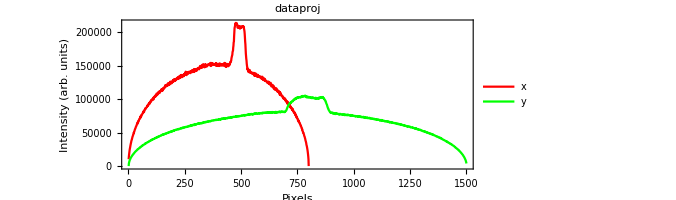

```mathematica
{ListPlot[originalProj, PlotLabel ->  "Signal Image",Frame -> True, FrameLabel -> {"Pixels","Intensity (arb. units)"}, PlotLegends -> LineLegend[{Red,Green},{"x","y"}]],ListPlot[MaskProj, PlotLabel -> "Mask Image",Frame -> True, FrameLabel -> {"Pixels","Intensity (arb. units)"}, PlotLegends -> LineLegend[{Red,Green},{"x","y"}]],ListPlot[dataproj,PlotLabel -> "dataproj",Frame -> True, FrameLabel -> {"Pixels","Intensity (arb. units)"}, PlotLegends -> LineLegend[{Red,Green},{"x","y"}]]}
```

NPOINT scaling with no backgroun dimage

97.4976

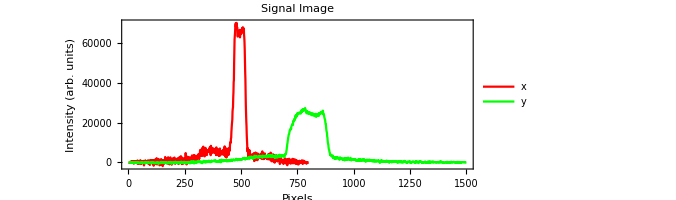

```mathematica
NPOINT=10;
dxs=dataproj⟦1⟧⟦1;;NPOINT⟧⟦All,2⟧;
dxe=dataproj⟦1⟧⟦-NPOINT;;-1⟧⟦All,2⟧;
dys=dataproj⟦2⟧⟦1;;NPOINT⟧⟦All,2⟧;
dye=dataproj⟦2⟧⟦-NPOINT;;-1⟧⟦All,2⟧;
mxs=MaskProj⟦1⟧⟦1;;NPOINT⟧⟦All,2⟧;
mxe=MaskProj⟦1⟧⟦-NPOINT;;-1⟧⟦All,2⟧;
mys=MaskProj⟦2⟧⟦1;;NPOINT⟧⟦All,2⟧;
mye=MaskProj⟦2⟧⟦-NPOINT;;-1⟧⟦All,2⟧;
p1=Join[dxs,dxe,dys,dye];
p2=Join[mxs,mxe,mys,mye];
bestscaling=i/.NMinimize[RootMeanSquare[i p2-p1],i]⟦2⟧
ttt=OrigImageCut mask0- bestscaling  mask0;
ListPlot[getXYProj2D[ttt], PlotLabel ->  "Signal Image",Frame -> True, FrameLabel -> {"Pixels","Intensity (arb. units)"}, PlotLegends -> LineLegend[{Red,Green},{"x","y"}]]
```

```mathematica
p1
```

{10322.,14582.,17669.,20427.,23119.,25484.,27211.,28960.,31053.,32654.,30680.,29161.,27317.,25326.,23137.,20538.,17676.,14372.,10201.,99.,97.,3976.,5714.,6907.,7982.,9051.,9866.,10513.,11310.,12063.,12846.,12080.,11417.,10581.,9961.,9146.,8092.,6916.,5711.,3973.}

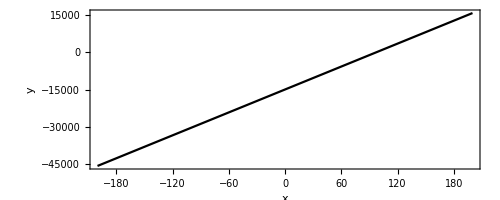

```mathematica
ListPlot[Table[{i,Mean[i p2-p1]},{i,-200,200,50}]]
```

```mathematica
p1
```

{10322.,14582.,17669.,20427.,23119.,25484.,27211.,28960.,31053.,32654.,30680.,29161.,27317.,25326.,23137.,20538.,17676.,14372.,10201.,99.,97.,3976.,5714.,6907.,7982.,9051.,9866.,10513.,11310.,12063.,12846.,12080.,11417.,10581.,9961.,9146.,8092.,6916.,5711.,3973.}

```mathematica
(*solve for y = 0 to give th eoptimum fit*)
twopoints=Table[{i,Mean[i p2-p1]},{i,0,1,1}]
```

{{0,-14954.8},{1,-14801.3}}

```mathematica
(twopoints⟦2,2⟧-twopoints⟦1,2⟧)/200 x-
```

```mathematica
(14945.8 1)/(twopoints⟦2,2⟧-twopoints⟦1,2⟧)
```

```mathematica
twopoints⟦2,2⟧-twopoints⟦1,2⟧
```

153.45

153.45

dot product mometn implmentation check

```mathematica
projs=getXYProj2D[ttt];
```

```mathematica
{getMoment1D[projs⟦1⟧⟦All,1⟧,1],√getMoment1D[projs⟦1⟧⟦All,1⟧,2]}
{getMoment1D[projs⟦2⟧⟦All,1⟧,1],√getMoment1D[projs⟦2⟧⟦All,1⟧,2]}
```

{533.667,188.679}

{1000.33,353.671}

320400

```mathematica
N@((projs⟦1⟧⟦All,1⟧.Range@Length@projs⟦1⟧⟦All,1⟧)/Total[projs⟦1⟧⟦All,1⟧])
```

533.667

```mathematica
Range@Length@projs⟦1⟧⟦All,1⟧.projs⟦1⟧⟦All,1⟧
```

170986800